# The Mathematics of Black Shells

## The code blocks in this notebook present the mathematics of the black shells as they appear in three primary sources: 1. Black Holes as Bubbles of AdS by Danielsson et al., 2017 [1] 2. Dynamics and Observational Signatures of Shell-like Black Hole Mimickers, by Danielsson et al., 2021 [2] 3. Stable gravastars — an alternative to black holes? by Visser and Wiltshire, 2004 [the VW Paper] There are three groups of code blocks: 1. The first group treats the general mathematics of black shells such as deriving the potential and density components. This relies heavily on the VW paper to verify the general equation for the potential. The equations in this section refer to equations in [1] 2. The second group is an implementation of the linearized stability analysis shown in Appendix B of [2]. 3. The third group implements the time-domain evolutions of the black shell dynamics as presented in [2]. All details can be found in my paper “Black Shells on the Edge of Collapse”

## General Mathematics of Black Shells: results largely checked with [VW Paper]

```mathematica
(* ::Section::1. Clear& define symbols/coords*)
ClearAll["Global`*"];
coords={t,r,θ,ϕ};
M=.;k=.;R=.;r=.;  (*M=.;ℓ=.;R=.;r=.;*)

(* ::Section::2. Metric functions and 4×4 metrics*)
fIn[x_]:=1+k*x^2;        (*AdS interior* 1+x^2/ℓ^2)*)
fOut[x_]:=1-2 M/x;         (*Schwarzschild exterior*)

gIn=DiagonalMatrix[{-fIn[r],1/fIn[r],r^2,r^2 Sin[θ]^2}];
gOut=DiagonalMatrix[{-fOut[r],1/fOut[r],r^2,r^2 Sin[θ]^2}];

(* ::Section::3. Christoffel symbols Γ^ρ_{μν}*)
GammaIn=Table[Simplify[1/2 Sum[Inverse[gIn][[σ,ρ]]*(D[gIn[[σ,μ]],coords[[ν]]]+D[gIn[[σ,ν]],coords[[μ]]]-D[gIn[[μ,ν]],coords[[σ]]]),{σ,1,4}]],{ρ,1,4},{μ,1,4},{ν,1,4}];
GammaOut=Table[Simplify[1/2 Sum[Inverse[gOut][[σ,ρ]]*(D[gOut[[σ,μ]],coords[[ν]]]+D[gOut[[σ,ν]],coords[[μ]]]-D[gOut[[μ,ν]],coords[[σ]]]),{σ,1,4}]],{ρ,1,4},{μ,1,4},{ν,1,4}];

(* ::Section::4. Unit normals (covariant)*)
nInCov={0,1/Sqrt[fIn[R]],0,0};
nOutCov={0,1/Sqrt[fOut[R]],0,0};

(* ::Section::5. Orthonormal shell tetrad (proper-time gauge)*)
eTauHatIn={1/Sqrt[fIn[R]],0,0,0};
eTauHatOut={1/Sqrt[fOut[R]],0,0,0};
eThetaHat={0,0,1/R,0};
ePhiHat={0,0,0,1/(R Sin[θ])};

(* ::Section::6. ∇_μ n_ν->4×4 arrays nablaIn,nablaOut*)
nablaIn=Table[Simplify[D[nInCov[[ν]],coords[[μ]]]-Sum[GammaIn[[σ,μ,ν]]*nInCov[[σ]],{σ,1,4}]],{μ,1,4},{ν,1,4}];
nablaOut=Table[Simplify[D[nOutCov[[ν]],coords[[μ]]]-Sum[GammaOut[[σ,μ,ν]]*nOutCov[[σ]],{σ,1,4}]],{μ,1,4},{ν,1,4}];

(* ::Section::7. Extrinsic curvature in ortho-frame->3×3 lists KIn,KOut*)
eListIn={eTauHatIn,eThetaHat,ePhiHat};
eListOut={eTauHatOut,eThetaHat,ePhiHat};

KIn=Table[Simplify[Sum[eListIn[[α,i]]*nablaIn[[i,j]]*eListIn[[β,j]],{i,1,4},{j,1,4}]/. r->R],{α,1,3},{β,1,3}];
KOut=Table[Simplify[Sum[eListOut[[α,i]]*nablaOut[[i,j]]*eListOut[[β,j]],{i,1,4},{j,1,4}]/. r->R],{α,1,3},{β,1,3}];
Print["Ext. curvature of interior: ",KIn] 
Print["Ext. curvature of exterior: ",KOut] 
(* ::Section::8. Jump ΔK=KOut-KIn and induced metric h_ab->3×3*)
dK=Simplify[KOut-KIn];
hOut3=Table[Simplify[eListOut[[i]].gOut.eListOut[[j]]/. r->R],{i,1,3},{j,1,3}];
hInv3=Simplify[Inverse[hOut3]];
Print["Jump ΔK=KOut-KIn: ",dK] 
Print["Outer induced metric h_ab: ",hOut3] 
Print["Inner induced metric h_ab: ",hInv3]

(* ::Section::9. Surface-stress S_ab=-1/(8π)(dK_ab-h_ab Tr[dK])*)
trK=Simplify[Tr[hInv3.dK]];
Ssurf=Simplify[-(1/(8 π)) (dK-hOut3 trK)];
Print["Surface-stress S_ab: ",Ssurf] 

(* ::Section::10. Extract σ=-S^τ_τ and p=S^θ_θ=S_{θθ}/R^2*)
sigma[r_,k_,M_]=FullSimplify[Ssurf[[1,1]]/. R->r];
p[r_,k_,M_]=FullSimplify[Ssurf[[2,2]]/. R->r];

(* ::Section::11. Display Eqs (2.1),(2.2)*)
Print["Surface energy density: ",sigma[r,k,M]//TraditionalForm]
Print["Surface Pressure: ",p[r,k,M]//TraditionalForm]
```

Ext. curvature of interior: {{-(k R)/(√(1+k R^2)),0,0},{0,(√(1+k R^2))/R,0},{0,0,(√(1+k R^2))/R}}

Ext. curvature of exterior: {{-M/(√(1-(2 M)/R) R^2),0,0},{0,(√(1-(2 M)/R))/R,0},{0,0,(√(1-(2 M)/R))/R}}

Jump ΔK=KOut-KIn: {{-M/(√(1-(2 M)/R) R^2)+(k R)/(√(1+k R^2)),0,0},{0,(√(1-(2 M)/R)-√(1+k R^2))/R,0},{0,0,(√(1-(2 M)/R)-√(1+k R^2))/R}}

Outer induced metric h_ab: {{-1,0,0},{0,1,0},{0,0,1}}

Inner induced metric h_ab: {{-1,0,0},{0,1,0},{0,0,1}}

Surface-stress S_ab: {{(-√(1-(2 M)/R)+√(1+k R^2))/(4 π R),0,0},{0,-(-M/(√(1-(2 M)/R) R^2)+(k R)/(√(1+k R^2))+(-√(1-(2 M)/R)+√(1+k R^2))/R)/(8 π),0},{0,0,-(-M/(√(1-(2 M)/R) R^2)+(k R)/(√(1+k R^2))+(-√(1-(2 M)/R)+√(1+k R^2))/R)/(8 π)}}

Surface energy density: (√(k r^2+1)-√(1-(2 M)/r))/(4 π r)

Surface Pressure: (-r √(k r^2+1)-(k r^3)/(√(k r^2+1))+r √(1-(2 M)/r)+M/(√(1-(2 M)/r)))/(8 π r^2)

```mathematica
(*2) Series-expand for large k up to O(k^(-1/2))*)
serSigma=Series[sigma[r,k,M],{k,Infinity,1}]//Normal;
serP=Series[p[r,k,M],{k,Infinity,0}]//Normal;
R0 = 9M/4;

(*4) Display the final expanded form*)
Print["----------------------------------------------"];
Print["--Final Expanded Forms--"];
Print["----------------------------------------------"];
Print["\n-The energy density and pressure in large k apprximation--"];
Print["surface energy in large k, small L approx. ",serSigma//TraditionalForm]
Print["surface pressure in large k, small L approx. ",serP//TraditionalForm]

Print["----------------------------------------------"];
Print["\n-Taking the lowest-order (in r) first radial derivatives and setting r = 9M/4--"];
Print["----------------------------------------------"];
dserSigma=FullSimplify[D[serSigma-(√(k r^2))/(8 π k r^3),r]/. r->R0];
dserP=FullSimplify[D[serP,r]/. r-> R0];

Print["----------------------------------------------"];
Print["surface energy in large k at r = 9M/4.:  ",dserSigma//TraditionalForm]
Print["surface pressure in large k at r = 9M/4:  ",dserP//TraditionalForm]

Print["----------------------------------------------"];
Print["\n-Taking the second-order radial derivative at setting r = 9M/4--"];
Print["----------------------------------------------"];
ddserSigma = FullSimplify[D[serSigma,{r,2}]]; (*-(√(k r^2))/(8 π k r^3)*)
Print["2nd order radial derivative of energy density:  ",ddserSigma//TraditionalForm]
Print["2nd order radial derivative of energy density at 9M/4:  ",ddserSigma/. r->R0//TraditionalForm]
```

----------------------------------------------

--Final Expanded Forms--

----------------------------------------------

-The energy density and pressure in large k apprximation--

surface energy in large k, small L approx. (√(k r^2))/(4 π r)+(√(k r^2))/(8 π k r^3)-(√((r-2 M)/r))/(4 π r)

surface pressure in large k, small L approx. (r-M)/(8 π r^2 √((r-2 M)/r))-(k r)/(4 π √(k r^2))

----------------------------------------------

-Taking the lowest-order (in r) first radial derivatives and setting r = 9M/4--

----------------------------------------------

----------------------------------------------

surface energy in large k at r = 9M/4.:  -4/(81 π M^2)

surface pressure in large k at r = 9M/4:  -14/(81 π M^2)

----------------------------------------------

-Taking the second-order radial derivative at setting r = 9M/4--

----------------------------------------------

2nd order radial derivative of energy density:  ((3 √(k r^2))/k+(r (-15 M^2+12 M r-2 r^2))/(√(1-(2 M)/r) (r-2 M)))/(4 π r^5)

2nd order radial derivative of energy density at 9M/4:  (256 ((27 √(k M^2))/(4 k)+(405 M^2)/8))/(59049 π M^5)

```mathematica
(*3*)(*break down of shell energy physics into three components: gas, stiff matter, and brane*)
ClearAll["Global`*"];

(*ClearAll[k,M,r,rhoB,pB,tau,rhoG,rhoS];*)
rhoB[r_]:=(1-Sqrt[1-2 M/r])/(4 Pi r);  (*Eq 2.11 derived in the previous code*)
pB[r_]:=rhoB[r]/2;                       (*Eq 2.12 derived in the previous code*)

term1=Sqrt[k]/(4 Pi)+1/(8 Pi Sqrt[k] r^2)-1/(4 Pi r);  (*RHS (2.14) minus ρB*)
term2=-Sqrt[k]/(4 Pi)+1/(8 Pi r);      (*RHS (2.15) minus pB*)

eq14=tau+rhoG+rhoS==term1+rhoB[r];  (*(2.14)*)
eq15=-tau+rhoG/2+rhoS==term2+pB[r];  (*(2.15)*)

(*2) Sum the two equations⇒eliminates τ*)
eqSum=Simplify[eq14+eq15];
(*eqSum is 3/2 rhoG+2 rhoS==term1+term2+rhoB[r]+pB[r]*)

(*3) Isolate the 1/Sqrt[k] piece in term1+term2*)
sumRHS=Simplify[term1+term2+rhoB[r]+pB[r]];
(*sumRHS=1/(8 π √k r^2)+(rhoB[r]+pB[r])-1/(8 π r)*)

(*4) Extract rhoS, *including*the 1/Sqrt[k] factor*)
coeff1=Coefficient[sumRHS,1/Sqrt[k]];
rhoSsol=Simplify[(coeff1/2)*(1/Sqrt[k])];   (*now=1/(16 π √k r^2)*)

(*5) Solve for rhoG*)
rhoGexpr=Simplify[(sumRHS-2 rhoSsol)*(2/3)];

(*6) Solve for tau*)
tauExpr=Simplify[term1+rhoB[r]-rhoGexpr-rhoSsol];

(*7) Display*)
Print["----------------------------------------------"];
Print["Energy Components"]
Print["----------------------------------------------"];

Print["stiff matter: ",rhoSsol//TraditionalForm]
Print["relativistic gas: ",rhoGexpr//TraditionalForm]
Print["brane tension: ",tauExpr//TraditionalForm]
 
(*8 ▹ first radial derivatives with the flux-freezing condition*)
Print["----------------------------------------------"];
Print["\n-First radial derivatives of density components with flux-freezing condition k->16/(81 M)"];
Print["----------------------------------------------"];
R0=9 M/4;                        (*Buchdahl radius*)
fluxRule=k->16/(81 M);            (*k(r) so that k r=4/3*)
fOut[x_]:=1-2 M/x;         (*Schwarzschild exterior*)

(*insert k(r) BEFORE differentiating-------------------------*)
rhoS[r_]=Simplify[rhoSsol/. fluxRule];
rhoG[r_]=Simplify[rhoGexpr/. fluxRule];
rhoTau[r_]=Simplify[tauExpr/. fluxRule];

drhoS=FullSimplify[D[rhoS[r],r]];
drhoG=FullSimplify[D[rhoG[r],r]];
drhoTau=FullSimplify[D[rhoTau[r],r]];

Print["\n---  First radial derivatives after inserting k(r) condition--"];
Print["∂_r ρ_s(r)   = ",TraditionalForm@drhoS];
Print["∂_r ρ_g(r)   = ",TraditionalForm@drhoG];
Print["∂_r ρ_τ(r)   = ",TraditionalForm@drhoTau];

(*evaluate at r=R0-----------------------------------------*)
numDrhoS=FullSimplify[drhoS/. r->R0];
numDrhoG=FullSimplify[drhoG/. r->R0];
numDrhoTau=FullSimplify[drhoTau/. r->R0];

Print["\n---  numerical values at r = 9 M / 4  -------------------"];
Print["ρ_s'(R0)   = ",numDrhoS];
Print["ρ_g'(R0)   = ",numDrhoG];
Print["ρ_τ'(R0)   = ",numDrhoTau];

Print["\n---  sanity check on the sum of the density components  ----------------"];
Print["check: ρ_τ'+ρ_g' = ",FullSimplify[numDrhoTau+numDrhoG]];
Print["check: ρ_τ'+ρ_g'+ρ_s' = ",FullSimplify[numDrhoTau+numDrhoG+numDrhoS]];
(*---------------------------------------------------------------*)(*11 ▹ First radial derivatives and their numerical values (no flux-freezing conditions)*)
(*---------------------------------------------------------------*)
Print["----------------------------------------------"]
Print["\n---  First radial derivatives analysis with no flux-freezing--"];
Print["----------------------------------------------"]
(*a) symbolic first derivatives*)
drhoSno=FullSimplify[D[rhoSsol,r]];
drhoGno=FullSimplify[D[rhoGexpr,r]];
drhoTauno=FullSimplify[D[tauExpr,r]];

Print["\n---  First radial derivative  ----------------"];
Print["∂_r ρ_s(r)   = ",TraditionalForm[drhoSno]];
Print["∂_r ρ_g(r)   = ",TraditionalForm[drhoGno]];
Print["∂_r ρ_τ(r)   = ",TraditionalForm[drhoTauno]];

(*b) evaluate at the Buchdahl radius R0=9 M/4*)
kRule=k->16/(81 M);                (*equilibrium:k R0=4/9*)

numDrhoSno=FullSimplify[drhoSno/. r->R0/. kRule];
numDrhoGno=FullSimplify[drhoGno/. r->R0/. kRule];
numDrhoTauno=FullSimplify[drhoTauno/. r->R0/. kRule];

Print["\n---  numerical values at r = 9 M / 4 and k->16/(81 M)  ----------------"];
Print["ρ_s'(R0) = ",numDrhoSno];
Print["ρ_g'(R0) = ",numDrhoGno];
Print["ρ_τ'(R0) = ",numDrhoTauno];

(*sanity check:sum of the three derivatives must vanish---------*)
Print["\n---  equilibrium consistency check on energy and pressure ---"];
Print["ρ_τ' + ρ_g'  = ",FullSimplify[numDrhoTauno+numDrhoGno]]
Print["-ρ_τ' + 1/2 ρ_g'  = ",FullSimplify[-numDrhoTauno+ numDrhoGno/2]]
Print["ρ_τ' + ρ_g' + ρ_s'  = ",FullSimplify[numDrhoTauno+numDrhoGno+numDrhoSno]]

(*--------------------------------------------------------------*)
(*9 ▹ Unruh temperature (shell frame& infinity)*)
(*--------------------------------------------------------------*)
Print["----------------------------------------------"];
Print["\n--analysis of the Unruh temperature and its relation to the radial derivative of the gas"];
Print["----------------------------------------------"];
(*proper 4-acceleration of a static observer just outside shell*)
aLocal[r_]=Simplify[(M/r^2)/Sqrt[1-2 M/r]];
TUnruh[r_]=aLocal[r]/(2 π);                        (*shell frame*)
dTUnruh=FullSimplify[D[TUnruh[r],r]];

Print["\n---Local Unruh temp. and its radial derivative--"];
Print["Unruh temp.   = ",TraditionalForm@TUnruh[r]];
Print["radial derivative of Unruh temp.  = ",TraditionalForm@dTUnruh];

Print["\n---Local Unruh temp. and its radial derivative @ 9M/4--"];
Print["local  T_U (shell frame) = ", Simplify[TUnruh[r]/. r->R0]];
Print["local derivative of  T_U (shell frame) = ", Simplify[dTUnruh/. r->R0]];
Print["∂_T/T  = ", Simplify[dTUnruh/TUnruh[r]/. r->R0]];

Toutside=FullSimplify[TUnruh[R0] Sqrt[fOut[R0]](*red-shifted*)];
Print["asympt. T_∞ (static observer) = ",TraditionalForm@Toutside,"  (= 8 /(81 π M))"];
```

----------------------------------------------

Energy Components

----------------------------------------------

stiff matter: 1/(16 π √k r^2)

relativistic gas: (2-3 √(1-(2 M)/r))/(12 π r)

brane tension: (12 √k r^2+3/(√k)-8 r)/(48 π r^2)

----------------------------------------------

-First radial derivatives of density components with flux-freezing condition k->16/(81 M)

----------------------------------------------

---  First radial derivatives after inserting k(r) condition--

∂_r ρ_s(r)   = -9/(32 π √(1/M) r^3)

∂_r ρ_g(r)   = (r (3-2 √(1-(2 M)/r))-9 M)/(12 π r^3 √(1-(2 M)/r))

∂_r ρ_τ(r)   = (16 r-27/(√(1/M)))/(96 π r^3)

---  numerical values at r = 9 M / 4  -------------------

ρ_s'(R0)   = -(2 (1/M)^(5/2))/(81 π)

ρ_g'(R0)   = -20/(243 M^2 π)

ρ_τ'(R0)   = (8-6 √(1/M))/(243 M^2 π)

---  sanity check on the sum of the density components  ----------------

check: ρ_τ'+ρ_g' = -(2 (2+√(1/M)))/(81 M^2 π)

check: ρ_τ'+ρ_g'+ρ_s' = -(4 (1+√(1/M)))/(81 M^2 π)

----------------------------------------------

---  First radial derivatives analysis with no flux-freezing--

----------------------------------------------

---  First radial derivative  ----------------

∂_r ρ_s(r)   = -1/(8 π √k r^3)

∂_r ρ_g(r)   = (r (3-2 √(1-(2 M)/r))-9 M)/(12 π r^3 √(1-(2 M)/r))

∂_r ρ_τ(r)   = -(3/(√k)-4 r)/(24 π r^3)

---  numerical values at r = 9 M / 4 and k->16/(81 M)  ----------------

ρ_s'(R0) = -(2 (1/M)^(5/2))/(81 π)

ρ_g'(R0) = -20/(243 M^2 π)

ρ_τ'(R0) = (8-6 √(1/M))/(243 M^2 π)

---  equilibrium consistency check on energy and pressure ---

ρ_τ' + ρ_g'  = -(2 (2+√(1/M)))/(81 M^2 π)

-ρ_τ' + 1/2 ρ_g'  = (2 (-3+√(1/M)))/(81 M^2 π)

ρ_τ' + ρ_g' + ρ_s'  = -(4 (1+√(1/M)))/(81 M^2 π)

----------------------------------------------

--analysis of the Unruh temperature and its relation to the radial derivative of the gas

----------------------------------------------

---Local Unruh temp. and its radial derivative--

Unruh temp.   = M/(2 π r^2 √(1-(2 M)/r))

radial derivative of Unruh temp.  = (M (3 M-2 r))/(2 π r^3 √(1-(2 M)/r) (r-2 M))

---Local Unruh temp. and its radial derivative @ 9M/4--

local  T_U (shell frame) = 8/(27 M π)

local derivative of  T_U (shell frame) = -64/(81 M^2 π)

∂_T/T  = -8/(3 M)

asympt. T_∞ (static observer) = 8/(81 π M)  (= 8 /(81 π M))

```mathematica
(*4*)(*Evaluate energy components at critical radius*)

(*ClearAll["Global`*"];*)
ClearAll[k,M,r];
rhoB[r_]:=(1-Sqrt[1-2 M/r])/(4 Pi r);                     (*Eq 2.11*)
pB[r_]:=(((1-M/r)/Sqrt[1-2 M/r])-1)/(8 Pi r);         (*Eq 2.12*)

(*2) Solve pB(r)==.bd rhoB(r) for the unique r*)
rSol=Solve[pB[r]==rhoB[r]/2,r];
Rcrit=r/. First[rSol];   (*the one physical solution*)

(*3) Define shell quantities (Eqs 2.16–2.18)*)
rhoS[r_]:=1/(16 Pi Sqrt[k] r^2);
rhoG[r_]:=rhoB[r]-1/(12 Pi r);
tau[r_]:=Sqrt[k]/(4 Pi)-1/(6 Pi r)+1/(16 Pi Sqrt[k] r^2);

(*4) Evaluate at the critical radius*)
rhoScrit=FullSimplify[rhoS[Rcrit]];
rhoGcrit=FullSimplify[rhoG[Rcrit]];
tauCrit=FullSimplify[tau[Rcrit]];
(*4) Evaluate at the critical radius and k=16/(81 M)*)
kRule=k->16/(81 M);
rhoScritk=FullSimplify[rhoS[Rcrit]/. kRule];
rhoGcritk=FullSimplify[rhoG[Rcrit]/. kRule];
tauCritk=FullSimplify[tau[Rcrit]/. kRule];


(*5) Display the results*)
Print["---------------------------------------------------------"];

Print["critical radius, stiff matter, gas, brane @r-->9M/4:",
{Rcrit,rhoScrit,rhoGcrit,tauCrit}//TraditionalForm]
Print["---------------------------------------------------------"];

Print["---------------------------------------------------------"];

Print["critical radius, stiff matter, gas, brane @r-->9M/4 and k-->16/(81M):",
{kRule,rhoScritk,rhoGcritk,tauCritk}//TraditionalForm]
Print["---------------------------------------------------------"];
```

Solve::fdimc: When parameter values satisfy the condition M==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

---------------------------------------------------------

critical radius, stiff matter, gas, brane @r-->9M/4:{(9 M)/4,1/(81 π √k M^2),1/(27 π M),(81 √k M^2+4/(√k)-24 M)/(324 π M^2)}

---------------------------------------------------------

---------------------------------------------------------

critical radius, stiff matter, gas, brane @r-->9M/4 and k-->16/(81M):{k→16/(81 M),(1/M)^(3/2)/(36 π),1/(27 π M),(3 √(1/M) (4 M+1)-8)/(108 π M)}

---------------------------------------------------------

```mathematica
(*Black–shell effective potential from Eq 2.22: General approach*)
(*we solve directly for the dynamic potential and then reduce it to the static case*)
(*Results verified against VW paper (Gravastars as alternatives to black holes): equations 17 and 40*)
(*1 ▸ housekeeping*)
(*ClearAll[R,M,k,sigma,Vcal,fOut,fIn,VppCrit,Vcrit,Vpp, V]*)
ClearAll["Global`*"];

(*2 ▸ Schwarzschild (outside) and AdS (inside) metric functions*)
fOut[R_]:=1-2 M/R                  (*1-2M/R*)
fIn[R_]:=1+k^2 R^2                (*1+k^2 R^2*)

(*3 ▸ Equation (2.22) (σ≡surface–energy density of the shell)*)
eq22=Sqrt[fIn[R]-2 Vcal]-Sqrt[fOut[R]-2 Vcal]-4 Pi sigma R==0;

(*4 ▸ Solve (square both sides twice is what Solve does internally) Ref. VW paper*)
solVcal=Solve[eq22,Vcal,Reals]    (*two algebraic roots appear*);
(*Print["roots= ", solVcal];*)
(*5 ▸ pick the root that reproduces the standard junction–condition sign;
this is the one that is continuous in the k->0 (flat‑inside) limit*)
VcalPhys=Vcal/. First@solVcal;    (*the “+” or “−” root–check!*);

(*6 ▸ switch to coding convention V:=2 𝓥*)
V[R_]=FullSimplify[2 VcalPhys](*Assumptions->{R>2 M,k>0,sigma>0}]*);

(*7 ▸ sanity checks*)
(*• the static shell satisfies V==0*)
dotR2=-V[R]; 
   (*by definition of the effective potential*)
FullSimplify[V[R]/. R->(9 M/4),Assumptions->{k>0,sigma>0}];

(*• second derivative at Buchdahl radius:should be negative (instability)*)
Vpp=D[V[R],{R,2}]//Simplify;
VppG=Simplify[Vpp,Assumptions->{k>0,sigma>0}]; (*/. R->(9 M/4)*)
(*  ==>negative quantity at critical radius and critical sigma*)
(*8 ▸ print the final result***************************************)
Print["----------------------------------------------"];
Print["----Print the general potential and its 2nd derivative"];
Print["----------------------------------------------"];
Print["General Potential  V(R) = ",TraditionalForm[V[R]]];
Print["General V''(R)= ",TraditionalForm[VppG]];       (* <0->unstable*)

Rcrit=9 M/4;

(*Print results: later we'll see that V=0 and V''<0 at the critical raidus and critical sigma*)
vals={V[R]/. R->Rcrit(*,D[V[R],R]/. R->Rcrit*), D[V[R],{R,2}]/. R->Rcrit};
valss = FullSimplify[vals];
Print["----------------------------------------------"];
Print["---Print potential and its 2nd derivative at 9M/4---"];
Print["----------------------------------------------"];
Print["V, V'' @critical radius: ", valss]
```

----------------------------------------------

----Print the general potential and its 2nd derivative

----------------------------------------------

General Potential  V(R) = ConditionalExpression[-((k^2 R^3+2 M)^2)/(64 π^2 R^4 sigma^2)+(k^2 R^2)/2-M/R-4 π^2 R^2 sigma^2+1, ]

General V''(R)= ConditionalExpression[-(4 M R^3 (k^2+16 π^2 sigma^2)+R^6 (k^2-16 π^2 sigma^2)^2+40 M^2)/(32 π^2 R^6 sigma^2), ]

----------------------------------------------

---Print potential and its 2nd derivative at 9M/4---

----------------------------------------------

V, V'' @critical radius: {ConditionalExpression[5/9+(81 k^2 M^2)/32-((128+729 k^2 M^2)^2)/(6718464 M^2 π^2 sigma^2)-81/4 M^2 π^2 sigma^2, ],ConditionalExpression[k^2-128/(729 M^2)-(163840+729 k^2 M^2 (256+729 k^2 M^2))/(17006112 M^4 π^2 sigma^2)-8 π^2 sigma^2, ]}

----------------------------------------------

---Print General Potential and Energy Density---

----------------------------------------------

General potential: ConditionalExpression[1-M/R+(k^2 R^2)/2-((2 M+k^2 R^3)^2)/(64 π^2 R^4 σ^2)-4 π^2 R^2 σ^2, ]

General Density: ConditionalExpression[(-√(1-(2 M)/R-2 Vcal)+√(1+k^2 R^2-2 Vcal))/(4 π R), 2 (M+R Vcal)<R]

----------------------------------------------

---Print Critical Energy Density---

----------------------------------------------

Critical energy density: (-4+3 √(16+81 k^2 M^2))/(108 M π)

----------------------------------------------

---Print Potential @9M/4---

----------------------------------------------

Potential at critical density and radius: ConditionalExpression[0, √(16+81 k^2 M^2)≠4/3+9 k M]

----------------------------------------------

---Print 2nd Derivative of Potential @9M/4 and its sign---

----------------------------------------------

V'' @critical density and radius 9M/4: ConditionalExpression[(32 (-416-729 k^2 M^2+24 √(16+81 k^2 M^2)))/(81 M^2 (4-3 √(16+81 k^2 M^2))^2), √(16+81 k^2 M^2)≠4/3+9 k M]

Sign of V'' @σcrit&Rc (True if <0): ConditionalExpression[True, √(16+81 k^2 M^2)≠4/3+9 k M]

----------------------------------------------

---Print 2nd Derivative of Density @9M/4---

----------------------------------------------

σ'' @critical density and radius 9M/4: ConditionalExpression[(32 (8/(1-18 Vcal)^(3/2)+8/(√(1-18 Vcal))-√(1-18 Vcal)-(6 (32+243 k^2 M^2-64 Vcal) (-1+2 Vcal))/((16+81 k^2 M^2-32 Vcal)^(3/2))))/(2187 M^3 π), Vcal<1/18]

----------------------------------------------

---Print Potential vs. Radius---

----------------------------------------------

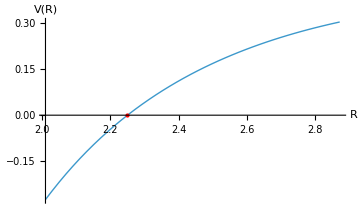

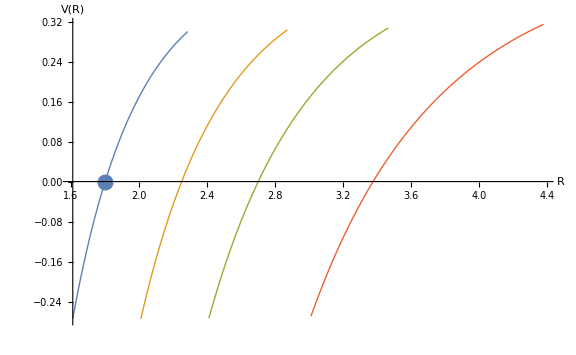

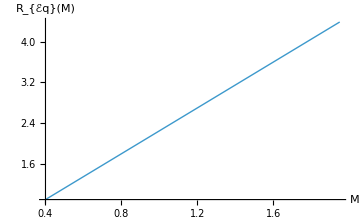

```mathematica
(*1 ▸ Putting it together*)
(*computing the potential, its derivatives, the critical sigma, then checking stability
of static case at critica radius*)
ClearAll["Global`*"];
(*ClearAll[R,M,k,σ,Vcal,V]*)

fOut[R_]:=1-2 M/R;        (*Schwarzschild*)
fIn[R_]:=1+k^2 R^2;      (*AdS*)

eq22=Sqrt[fIn[R]-2 Vcal]-Sqrt[fOut[R]-2 Vcal]-4 π σ R==0;

(*2 ▸ eliminate Vcal, σ,keep the root that is continuous as k->0*)
VcalPhys=Vcal/. Solve[eq22,Vcal,Reals][[1]];
V[R_]=FullSimplify[2 VcalPhys,Assumptions->{R>2 M,k>0,σ>0,M>0}];

σPhys=σ/. Solve[eq22,σ,Reals][[1]];
σGen[R_]=FullSimplify[σPhys,Assumptions->{R>2 M,k>0,σ>0,M>0}];

Print["----------------------------------------------"];
Print["---Print General Potential and Energy Density---"];
Print["----------------------------------------------"];

Print["General potential: ", V[R]]
Print["General Density: ", σGen[R]]

(*3 ▸ Buchdahl radius and critical surface tension*)
Rc=9 M/4;
σcritRule=Solve[Sqrt[fIn[Rc]]-Sqrt[fOut[Rc]]-4 π σ Rc==0,σ,Reals][[1]];
σcrit=FullSimplify[σ/. σcritRule,Assumptions->{M>0,k>0}];

Print["----------------------------------------------"];
Print["---Print Critical Energy Density---"];
Print["----------------------------------------------"];

Print["Critical energy density: ", σcrit]

(*4 ▸ checks:V(Rc)=0 and V''(Rc)<0*)
Vcrit=FullSimplify[V[Rc]/. σcritRule,Assumptions->{M>0,k>0}];
Print["----------------------------------------------"];
Print["---Print Potential @9M/4---"];
Print["----------------------------------------------"];

Print["Potential at critical density and radius: ", Vcrit]

Vpp=D[V[R],{R,2}]//FullSimplify;
VppCrit=FullSimplify[Vpp/. R->Rc/. σcritRule,Assumptions->{M>0,k>0}];
VppCrits= FullSimplify[VppCrit,Assumptions->{M>0,k>0}];

σpp=D[σGen[R],{R,2}]//FullSimplify;
σppCrit=FullSimplify[σpp/. R->Rc,Assumptions->{M>0,k>0}];
σppCrits= FullSimplify[σppCrit,Assumptions->{M>0,k>0}];


Print["----------------------------------------------"];
Print["---Print 2nd Derivative of Potential @9M/4 and its sign---"];
Print["----------------------------------------------"];

Print["V'' @critical density and radius 9M/4: ", VppCrits]
sign=Simplify[VppCrit<0];
Print["Sign of V'' @σcrit&Rc (True if <0): ",sign]

Print["----------------------------------------------"];
Print["---Print 2nd Derivative of Density @9M/4---"];
Print["----------------------------------------------"];
Print["σ'' @critical density and radius 9M/4: ", σppCrits]

(*5 ► choose numbers,fix σ to its critical value,and plot V(R)*)
(*pick any convenient positive numbers*)
Mval=1;        (*mass parameter*)
kval=0.1;      (*AdS curvature scale*)

(*critical surface density σ*that makes V(9M/4)=0*)
sigmaCritVal=σ/. (σcritRule/. {M->Mval,k->kval})[[1]];

(*numerical potential*)
Vnum[R_]=Evaluate[V[R]/. {M->Mval,k->kval,σ->sigmaCritVal}];
Print["----------------------------------------------"];
Print["---Print Potential vs. Radius---"];
Print["----------------------------------------------"];

(*plot from just outside the Schwarzschild radius 2M to,say,3M*)
Plot[Vnum[R],{R,2 Mval+0.01,3 Mval},PlotRange->All,AxesLabel->{"R","V(R)"},PlotStyle->Thick,Epilog->{Red,Point[{9 Mval/4,0}]},(*marks the critical point*)PlotLegends->Placed["V(R)",Above],ImageSize->Medium]

(*6 ► family of potentials V_M(R) for several masses*)
(*(each in its own colour,all sharing the same k)*)
kval=0.1;                   (*fixed AdS curvature*)
massList={0.8,1,1.2,1.5};    (*sample M values to display*)
colScheme=ColorData[97,"ColorList"];  (*nice categorical colours*)

potCurves=Table[Module[{Mval=M0,sigmaCrit=σ/. (σcritRule/. {M->M0,k->kval})[[1]],Vnum},Vnum[R_]=Evaluate@V[R]/. {M->Mval,k->kval,σ->sigmaCrit};
{Plot[Evaluate@Vnum[R],{R,2 Mval+.01,3 Mval},PlotRange->{Automatic,All},PlotStyle->{colScheme[[i]],Thick},AxesLabel->{"R","V(R)"},PlotLegends->None,Epilog->{colScheme[[i]],PointSize[0.02],Point[{9 Mval/4,0}]}],(*returns the graphics*)colScheme[[i]]}],{i,Length@massList},{M0,{massList[[i]]}}]//Flatten[#,1]&;

Show[potCurves[[All,1]],PlotRange->All,PlotLegends->Placed[Thread[Style[Row[{"M = ",massList}],colScheme[[;;Length@massList]]]],{0.85,0.9}],ImageSize->Large,GridLines->{{},{0}}]

(*7 ► equilibrium (Buchdahl) radius R_eq(M)=9 M/4*)
eqRadius[M_]:=9 M/4;
Plot[Evaluate@eqRadius[M],{M,First@massList/2,1.3 Last@massList},PlotStyle->Thick,AxesLabel->{"M",Row[{"R_{ℰq}(M)"}]},PlotRange->All,ImageSize->Medium]
```

## Appendix B of [2]: Implementation of the Linear Stability Analysis

---------------------------------------------

--General Density and Pressure of Shell--

---------------------------------------------

(√(1+ȧ^2+a^2 k)-√(1+ȧ^2-(2 M)/a))/(4 a π)

-((a k)/(√(1+ȧ^2+a^2 k))+(√(1+ȧ^2+a^2 k))/a+(-((1+ȧ^2) a)+M)/(a^(3/2) √(a+ȧ^2 a-2 M))+ä (1/(√(1+ȧ^2+a^2 k))-1/(√(1+ȧ^2-(2 M)/a))))/(8 π)

---------------------------------------------

--Static-Case Density and Pressure of Shell--

---------------------------------------------

(√(1+a^2 k)-√(1-(2 M)/a))/(4 a π)

-((a k)/(√(1+a^2 k))+(√(1+a^2 k))/a+(-a+M)/(√(a^3 (a-2 M))))/(8 π)

(2+√2)/(36 M π)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

---------------------------------------------

--General Potential--

---------------------------------------------

V(a) = (a^2 k)/2-4 π^2 a^2 σsymb^2-((a^3 k+2 M)^2)/(64 π^2 a^4 σsymb^2)-M/a+1

{rhoG', rhoS', rhoTau'} at R0 = {-20/(243 M^2 π),-8/(729 √k M^3 π),-(8 (1/(√k)-3 M))/(729 M^3 π)}

---------------------------------------------

Linear first-order equations:

---------------------------------------------

(8 α δR)/(27 M^2 π τu)+(3 α δT)/(8 τu)+(4 ⅈ δR ω)/(81 M^2 π)-(4 ⅈ β δR ω)/(81 M^2 π)+ⅈ δρg ω+(9 α δR ω^2)/(16 π τu)==0
-(8 α δR)/(27 M^2 π τu)-(3 α δT)/(8 τu)+(4 ⅈ β δR ω)/(81 M^2 π)+ⅈ δρτ ω-(9 α δR ω^2)/(16 π τu)==0
(16 ⅈ δR ω)/(729 √k M^3 π)+ⅈ δρs ω==0
(64 δR)/(81 M^2 π τu)+δT/τu+ⅈ δT ω+(3 δR ω^2)/(2 π τu)==0
-(112 δR)/(81 M^2)+(64 k δR)/((16+81 k M^2)^(3/2))+(64 δR)/(81 M^2 √(16+81 k M^2))-4 π δρg-8 π δρs+8 π δρτ+(64 ⅈ π δR ζ0 ω)/(9 M)-3 δR ω^2-(64 δR ω^2)/((16+81 k M^2)^(3/2))-(324 k M^2 δR ω^2)/((16+81 k M^2)^(3/2))==0

Linearised mode frequencies:

alternative method to derive the frequencies: much faster

end of alternative method

ω→0
ω→0
ω→0
ω→(ⅈ (-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu))/(12 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))-(-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)/(6 2^(2/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))+(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))/(12 2^(1/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))
ω→(ⅈ (-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu))/(12 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))+((1+ⅈ √3) (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2))/(12 2^(2/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))-((1-ⅈ √3) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))/(24 2^(1/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))
ω→(ⅈ (-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu))/(12 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))+((1-ⅈ √3) (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2))/(12 2^(2/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))-((1+ⅈ √3) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))/(24 2^(1/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))

....................................................................

root index: 4

ω→(ⅈ (-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu))/(12 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))-(-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)/(6 2^(2/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) ((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))+(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3+√(((4194304 ⅈ-127401984 ⅈ k M^2-859963392 ⅈ k^(3/2) M^3+1289945088 ⅈ k^2 M^4+17414258688 ⅈ k^(5/2) M^5+54419558400 ⅈ k^3 M^6-88159684608 ⅈ k^(7/2) M^7-595077871104 ⅈ k^4 M^8-1338925209984 ⅈ k^(9/2) M^9+1934917632 ⅈ k^(3/2) M^3 α-39182082048 ⅈ k^(5/2) M^5 α-264479053824 ⅈ k^3 M^6 α+198359290368 ⅈ k^(7/2) M^7 α+2677850419968 ⅈ k^4 M^8 α+9037745167392 ⅈ k^(9/2) M^9 α+297538935552 ⅈ k^3 M^6 α^2-3012581722464 ⅈ k^4 M^8 α^2-20334926626632 ⅈ k^(9/2) M^9 α^2+15251194969974 ⅈ k^(9/2) M^9 α^3+1019215872 ⅈ k^(3/2) M^2 π ζ0 τu-20639121408 ⅈ k^(5/2) M^4 π ζ0 τu-139314069504 ⅈ k^3 M^5 π ζ0 τu+104485552128 ⅈ k^(7/2) M^6 π ζ0 τu+1410554953728 ⅈ k^4 M^7 π ζ0 τu+4760622968832 ⅈ k^(9/2) M^8 π ζ0 τu-156728328192 ⅈ k^3 M^5 π α ζ0 τu+1586874322944 ⅈ k^4 M^7 π α ζ0 τu+10711401679872 ⅈ k^(9/2) M^8 π α ζ0 τu-48201307559424 ⅈ k^(9/2) M^8 π α^2 ζ0 τu-301989888 ⅈ k τu^2+1019215872 ⅈ k^(3/2) M τu^2+6115295232 ⅈ k^2 M^2 τu^2+20639121408 ⅈ k^(5/2) M^3 τu^2-170272751616 ⅈ k^3 M^4 τu^2-313456656384 ⅈ k^(7/2) M^5 τu^2+4760622968832 ⅈ k^(9/2) M^7 τu^2-4586471424 ⅈ k^(3/2) M α τu^2+116095057920 ⅈ k^(5/2) M^3 α τu^2+548549148672 ⅈ k^3 M^4 α τu^2-705277476864 ⅈ k^(7/2) M^5 α τu^2-7140934453248 ⅈ k^4 M^6 α τu^2-16067102519808 ⅈ k^(9/2) M^7 α τu^2+509607936 ⅈ k^(3/2) M β τu^2-10319560704 ⅈ k^(5/2) M^3 β τu^2-69657034752 ⅈ k^3 M^4 β τu^2+52242776064 ⅈ k^(7/2) M^5 β τu^2+705277476864 ⅈ k^4 M^6 β τu^2+2380311484416 ⅈ k^(9/2) M^7 β τu^2-39182082048 ⅈ k^3 M^4 α β τu^2+396718580736 ⅈ k^4 M^6 α β τu^2+2677850419968 ⅈ k^(9/2) M^7 α β τu^2-165112971264 ⅈ k^3 M^4 π^2 ζ0^2 τu^2+1671768834048 ⅈ k^4 M^6 π^2 ζ0^2 τu^2+11284439629824 ⅈ k^(9/2) M^7 π^2 ζ0^2 τu^2+50779978334208 ⅈ k^(9/2) M^7 π^2 α ζ0^2 τu^2-24461180928 ⅈ k^(5/2) M^2 π ζ0 τu^3+82556485632 ⅈ k^3 M^3 π ζ0 τu^3+247669456896 ⅈ k^(7/2) M^4 π ζ0 τu^3+835884417024 ⅈ k^4 M^5 π ζ0 τu^3-5642219814912 ⅈ k^(9/2) M^6 π ζ0 τu^3+41278242816 ⅈ k^3 M^3 π β ζ0 τu^3-417942208512 ⅈ k^4 M^5 π β ζ0 τu^3-2821109907456 ⅈ k^(9/2) M^6 π β ζ0 τu^3-17832200896512 ⅈ k^(9/2) M^6 π^3 ζ0^3 τu^3))^2+4 (-768 (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu) (324 k^(3/2) M^2 π ζ0+16 k τu-54 k^(3/2) M τu-27 k^(3/2) M β τu)+(-128+1296 k M^2+8748 k^(3/2) M^3-19683 k^(3/2) M^3 α+20736 k^(3/2) M^2 π ζ0 τu)^2)^3)))^(1/3))/(12 2^(1/3) (-32 τu+324 k M^2 τu+2187 k^(3/2) M^3 τu))

Testing Parameter Space for Large-m Limit for Root 4

Parameters: M0, β0, α0, ζcon, k0, τ0 5000|-0.2666|0.399998|0.1|1|0.03

ω->4 with given parameters: {ω→-9.4369×10^-15+0.00145317 ⅈ}

ω->5 with given parameters: {ω→0.+3.33301 ⅈ}

ω->6 with given parameters: {ω→9.54792×10^-15+0.0000362525 ⅈ}

Parameters: M0, β0, α0, ζcon, k0, τ0 5000|-0.2666|5/9|0.1|1|0.03

ω->4 with given parameters: {ω→-4.61853×10^-14-0.000671222 ⅈ}

ω->5 with given parameters: {ω→4.66294×10^-14+0.000075355 ⅈ}

ω->6 with given parameters: {ω→-2.22045×10^-16-8.33135 ⅈ}

Parameters: M0, β0, α0, ζcon, k0, τ0 5000|-0.2666|3|0.1|1|0.03

ω->4 with given parameters: {ω→-1.49214×10^-13-0.000163016 ⅈ}

ω->5 with given parameters: {ω→1.49214×10^-13+0.000137114 ⅈ}

ω->6 with given parameters: {ω→0.-191.66 ⅈ}

Parameters: M0, β0, α0, ζcon, k0, τ0 5000|0.8|0.45|0.1|1|0.03

ω->4 with given parameters: {ω→-2.21582×10^-11-0.0123067 ⅈ}

ω->5 with given parameters: {ω→2.14821×10^-11-5.30146×10^-6 ⅈ}

ω->6 with given parameters: {ω→6.76029×10^-13-0.403206 ⅈ}

Parameters: M0, β0, α0, ζcon, k0, τ0 5000|-0.2666|0.399998|0.3|1|10

ω->4 with given parameters: {ω→0.00415979+0.00521901 ⅈ}

ω->5 with given parameters: {ω→-0.00415979+0.00521901 ⅈ}

ω->6 with given parameters: {ω→-5.96311×10^-19+0.0000118263 ⅈ}

............Graphs..................

wave shape of root: 4

Real part of I(ω)

Set::setraw: Cannot assign to raw object 0.

Imaginary part of I(ω)

Real part of I(ω) with a masss range

Set::setraw: Cannot assign to raw object 0.

phase portrait with stability label of root 4

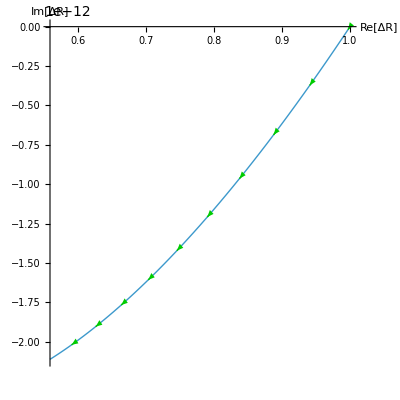

Contour Graph for α and M of root: 4

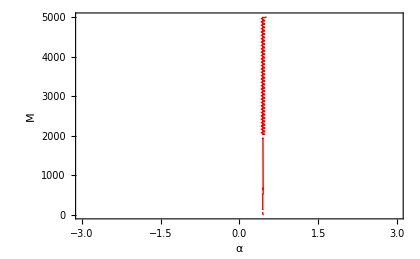

Contour Graph for α and β of root: 4

-Graphics-

Contour Graph for α and ζ0 of root: 4

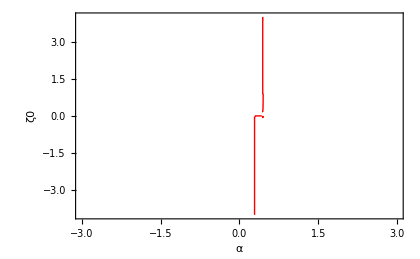

Contour Graph for α and τu of root: 4

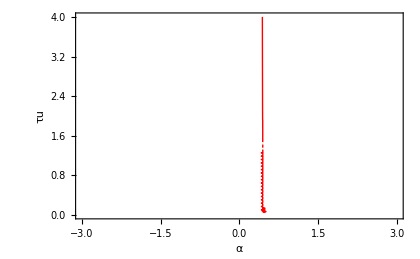

Part::pkspec1: The expression rootIndex cannot be used as a part specification.

ReplaceAll::reps: {freqRulesju⟦rootIndex⟧} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

Part::pkspec1: The expression rootIndex cannot be used as a part specification.

ReplaceAll::reps: {freqRulesju⟦rootIndex⟧} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

Part::pkspec1: The expression rootIndex cannot be used as a part specification.

ReplaceAll::reps: {freqRulesju⟦rootIndex⟧} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

```mathematica
(*Ju. Running The Most General Quasi-Static Perturbations*)
(*I fully reproduce the results obtained in Appendix B of Dynamics and Observational Signatures of Shell-Like Black Hole Mimickers*)
(*The mathematical derivation of the shell potential follows the VW paper*)

ClearAll["Global`*"];
Clear[σShell, pShell];
$Assumptions={M>0,k>0,a>2 M};
fIn[r_]:=1+k r^2;          (*AdS interior*)
fOut[r_]:=1-2 M/r;          (*Schwarzschild exterior*)

γIn[a_,ȧ_]:=Sqrt[ȧ^2+fIn[a]];
γOut[a_,ȧ_]:=Sqrt[ȧ^2+fOut[a]];

(*extrinsic curvature components—VW eqs.(22)-(24)*)
KθθIn[a_,ȧ_]:=γIn[a,ȧ]/a;
KθθOut[a_,ȧ_]:=-γOut[a,ȧ]/a;

KττIn[a_,ȧ_,ä_]:=-(ä+fIn'[a]/2)/γIn[a,ȧ]; (*KττIn[a_]:=-(add+fIn'[a]/2)/γIn[a];*)
KττOut[a_,ȧ_,ä_]:=(ä+fOut'[a]/2)/γOut[a,ȧ]; (*KττOut[a_]:=-(add+fOut'[a]/2)/γOut[a];*)

(*----------surface energy–density and pressure (genuine functions)----*)σShell[a_,ȧ_,ä_]:=Module[{ΔKθθ=KθθOut[a,ȧ]+KθθIn[a,ȧ],ΔKττ=KττOut[a,ȧ,ä]+KττIn[a,ȧ,ä],trΔK},trΔK=-ΔKττ+2 ΔKθθ;
Simplify[(ΔKττ+trΔK)/(8 π)]];

pShell[a_,ȧ_,ä_]:=Module[{ΔKθθ=KθθOut[a,ȧ]+KθθIn[a,ȧ],ΔKττ=KττOut[a,ȧ,ä]+KττIn[a,ȧ,ä],trΔK},trΔK=-ΔKττ+2 ΔKθθ;
Simplify[(-1)(-(ΔKθθ-trΔK))/(8 π)]];


Print["---------------------------------------------"]
Print["--General Density and Pressure of Shell--"]
Print["---------------------------------------------"]
Print[FullSimplify[σShell[a,ȧ,ä],$Assumptions]]
Print[FullSimplify[pShell[a,ȧ,ä],$Assumptions]]
(*-STATIC LIMIT-*rhoStatic=*)
Print["---------------------------------------------"]
Print["--Static-Case Density and Pressure of Shell--"]
Print["---------------------------------------------"]

FullSimplify[σShell[a,ȧ,ä]/.{ȧ->0,ä->0},$Assumptions]
FullSimplify[pShell[a,ȧ,ä]/.{ȧ->0,ä->0} ,$Assumptions]
cJump = FullSimplify[σShell[a,ȧ,ä]/.{a->9 M/4,ȧ->0,ä->0,k->16/(81 M^2)},$Assumptions]+ FullSimplify[pShell[a,ȧ,ä]/.{a->9 M/4,ȧ->0,ä->0,k->16/(81 M^2)} ,$Assumptions];
cJump = FullSimplify[cJump]


(*---symbolic surface tension (free function of a)------------*)
 
Clear[σsymb];

F[a_,v_] := γIn[a,v] - γOut[a,v] - 4 π a σsymb;

solAd = Solve[F[a,v]==0,v][[1]];
ȧ2=FullSimplify[(v/. solAd)^2,$Assumptions];
V[a_]:=FullSimplify[-ȧ2, $Assumptions];   (*so ȧ^2+V(a)=0*)

(*Critical surface tension σ★*)
aStar=9 M/4; (*Buchdahl radius*) 
(*σCritRule=Solve[Sqrt[fIn[aStar]]-Sqrt[fOut[aStar]]-4 π σ aStar==0,σ,Reals][[1]];  *) 
σCritRule=Solve[γIn[aStar,0] - γOut[aStar,0] - 4 π σ aStar==0,σ,Reals][[1]];                  
σCritRule;
σCrit=FullSimplify[σ/. σCritRule, $Assumptions];
σCrit;
(*Check V(a★)=0& V''(a★)<0*)
Vpp=D[V[a],{a,2}]//FullSimplify;
(*sign=Simplify[ReducedVpp[aStar]<0];*)

Vcrit = FullSimplify[V[a]/.{a ->aStar,v->0,σsymb->σCrit}, $Assumptions]; (* ä->0*)
VppCrit = FullSimplify[Vpp/.{a ->aStar,v->0, σsymb-> σCrit}, $Assumptions];
VppCritk = FullSimplify[VppCrit/.k->16/(81 M^2), $Assumptions];


Print["---------------------------------------------"]
Print["--General Potential--"]
Print["---------------------------------------------"]

Print["V(a) = ",TraditionalForm[FullSimplify[V[a]]]];
(*Print["---------------------------------------------"]
Print["--Critical Density, Potential@9M/4, V''@9M/4--"]
Print["---------------------------------------------"]

Print["σ★(a★) = ",σCrit];
Print["V(a★): ", TraditionalForm[FullSimplify[Vcrit]]]
Print["V''(a★): ", TraditionalForm[FullSimplify[VppCrit]]]
Print["V''(a★): ", TraditionalForm[FullSimplify[VppCritk]]] *)

(* ::Section::*)(*Linear perturbation with quasi–static flux (fixed)*)
Clear[ω,ε,δR,δρg,δρτ ,δρs,δT ,τu,α,β, linEqs,js, jLin];
Clear[R0,eqG,eqTau,eqS,mat,dispEq,freqRules,dKθθ,dKττ,trdK];
Clear[mat,dispEq,freqRules, eqs];
Clear[QR,QL,Vdot60];

 (*relaxation time-scale τ_u*)
$Assumptions=$Assumptions&&τu>0;
$Assumptions=$Assumptions&&Element[α|β,Re]; 

ω=Symbol["ω"];          (*complex frequency*)
ε=Symbol["ϵ"];        (*book-keeping parameter*)
(*one new symbol and a viscous-corrected pressure*)
ζ0=Symbol["ζ0"];            (*ζ₀–keep it symbolic*)
(*external flux parameters (kept symbolic)*)
xiU=Symbol["ξU"];
xiS=Symbol["ξS"];


R0 = 9M/4;
rhoG[a_]:=(2-3 Sqrt[1-2 M/a])/(12 π a);
rhoS[a_]:=1/(16 π Sqrt[k] a^2);
rhoTau[a_]:=Sqrt[k]/(4 π)-1/(6 π a)+1/(16 π Sqrt[k] a^2);
rhoB[a_]:=(1-Sqrt[1-2 M/a])/(4 π a);      (*binding term*)
pB[a_]:=rhoB[a]/2;
(*Unruh temperature*)
TU[a_]:=M/(2 π a^2 Sqrt[1-2 M/a]);
QR[a_,v_]:=Sqrt[fOut[a]+v^2];
QL[a_,v_]:=Sqrt[fIn[a]+v^2];

(*quick sanity check at Buchdahl radius*)

(*first radial derivatives at R0*)
drho=(D[#,a]/. a->R0)&/@{rhoG[a],rhoS[a],rhoTau[a]};
Print["{rhoG', rhoS', rhoTau'} at R0 = ",Simplify/@drho];

(*background: the setup follows the paper: Dynamics and Observational Signatures fo Shell-like Black Hole Mimickers*)
ρg0=rhoG[R0];
ρs0=rhoS[R0];
ρτ0=rhoTau[R0];
T0=TU[R0]//FullSimplify;          (*8/(27 π M)*)

(*perturbative ansatz*)
R[τ_]:=R0+ε δR Exp[I ω τ];
ρg[τ_]:=ρg0+ε δρg Exp[I ω τ];
ρs[τ_]:=ρs0+ε δρs Exp[I ω τ];
ρτ[τ_]:=ρτ0+ε δρτ Exp[I ω τ];
T[τ_]:=T0+ε δT Exp[I ω τ];   (*temperature perturbation ansatz*)

Rdot[τ_]:=D[R[τ],τ];
Rddot[τ_]:=D[R[τ],{τ,2}];

Pnet[τ_]:=ρg[τ]/2-ρτ[τ]+ρs[τ]-(2 ζ0 Rdot[τ])/R[τ];
Vdot60[a_,v_,P_,xiU_,xiS_]:=((3*a*k)*QR[a,v]-4 π*QL[a,v]*(a*(xiS^2+xiU^2)-4 P*QR[a,v]))/(2 (QL[a,v]-QR[a,v]))+(QL[a,v]*QR[a,v]-1-v^2)/(2 a);
(*Define the dynamical acceleration equation*)
Rddot2[τ_]:=Vdot60[R[τ],Rdot[τ],Pnet[τ],xiU,xiS];

(*proper acceleration and F, equations A1 and Fractional change in proper area*)
(*red-shifted static proper acceleration*)

aR[τ_]:=(4 π R[τ]^2(xiU^2+xiS^2)+2*Rddot[τ]*R[τ] +1-fOut[R[τ]])/(2*QR[R[τ],Rdot[τ]]*R[τ]); (*eq 67*)
(*aR[τ_]:=(M/R[τ]^2+Rddot[τ])/Sqrt[1-2 M/R[τ]+Rdot[τ]^2]; eq. A2*)
(*Farea[τ_]:=2 (Rdot[τ]/R[τ]-2M Rdot[τ]/(R[τ](R[τ]-2 M)));*) (*includes a relativistic red-shift correction*)
Farea[τ_]:=2 Rdot[τ]/R[τ];(*this maybe more suitable case*)

(*quasi-static flux j_u equation 88*)
(*js[τ_]:=3 ρg[τ] (α*D[aR[τ],τ]/aR[τ]+β*Farea[τ]/2); *)(*equation 86: setting alpha and beta = 1 gives us equation 85*)
js[τ_]:=3 ρg[τ] ( α/τu(aR[τ]/(2 π T[τ])-1)+β Farea[τ]/2); (*eq88*)

(*dynamical equations equations 78, 79*)
eqG=D[ρg[τ],τ]+(3/2) ρg[τ] Farea[τ]-js[τ]- (4 ζ0 (Rdot[τ])^2)/(R[τ])^2- xiS*xiU==0; (*equation 70*) 
eqTau=D[ρτ[τ],τ]+js[τ]==0;
eqS=D[ρs[τ],τ]+2ρs[τ]Farea[τ]==0;
eqT=D[T[τ],τ]-((aR[τ]/(2 π))-T[τ])/τu==0; (*ADD TEMPERATURE EVOLUTION (Eq.87)*)
eq60=D[R[τ],{τ,2}]-Rddot2[τ]==0; (*Eq.60 expressed as Vdot==...: either this formula or eqAccelFull can be used for the perturbation*)

(*---1. define the perturbed surface density via the curvature routine---*)
σPert[τ_]:=σShell[R[τ],Rdot[τ],Rddot[τ]];
Vdyn[τ_]:=V[R[τ]] /. {a->R[τ],σsymb->σPert[τ]};

eqM=γIn[R[τ],Rdot[τ]]-γOut[R[τ],Rdot[τ]]-4 π R[τ] (*σPert[τ]*)(ρg[τ]+ρs[τ]+ρτ[τ])==0;
(*Rdot[τ]^2+ 2Vdyn[τ]- 4 π R[τ]^2σPert[τ]+R[τ](Sqrt[1+k R[τ]^2]-1)*) (*Energy equation*)
(*γIn[R[τ],Rdot[τ]]-γOut[R[τ],Rdot[τ]]-4 π R[τ] (*σPert[τ]*)(ρg[τ]+ρs[τ]+ρτ[τ])*)

dKθθ=KθθOut[R[τ],Rdot[τ]]+KθθIn[R[τ],Rdot[τ]];
dKττ=KττOut[R[τ],Rdot[τ],Rddot[τ]]+KττIn[R[τ],Rdot[τ],Rddot[τ]];
trdK=-dKττ+2 dKθθ;
(*full Israel momentum equation (angular+radial pieces)-dKθθ+trdK+8 π Pnet[τ]==0;*)
eqAccelFull= 
-((γIn[R[τ],Rdot[τ]]-γOut[R[τ],Rdot[τ]])/R[τ]-(Rddot[τ]+fOut'[R[τ]]/2)/γOut[R[τ],Rdot[τ]]-(Rddot[τ]+fIn'[R[τ]]/2)/γIn[R[τ],Rdot[τ]]+8 π Pnet[τ])==0;


(*Israel momentum condition: frame-invariant momentum-junction condition*)

Print["---------------------------------------------"];
Print["Linear first-order equations:"];
Print["---------------------------------------------"];

residuals=({eqG,eqTau,eqS,eqT,eqM }/. Equal->Subtract)/. τ->0;          (*/. Equal->Subtract*)
residualsBg=residuals/. {a->R0}/.{xiS->0,xiU->0};                                             (*,k->16/(81 M^2),σsymb->σCrit*)(*/. {α->1,β->1}*)
linFirst3=SeriesCoefficient[residualsBg[[1;;4]],{ε,0,1}]//Expand;

(*resIsrael1=SeriesCoefficient[residualsBg[[5]],{ε,0,1}]/δR;*)
(*resIsrael2=SeriesCoefficient[residualsBg[[5]],{ε,0,2}]/δR;*)

resAccel=(eqAccelFull/. Equal->Subtract)/.{xiS->0,xiU->0}/. τ->0;
linAccel=SeriesCoefficient[resAccel,{ε,0,1}]//Expand;

reAccel=(eq60/. Equal->Subtract)/.{xiS->0,xiU->0}/. τ->0;
liAccel=SeriesCoefficient[reAccel,{ε,0,1}]//Expand;  

linEqs=Join[linFirst3,{linAccel}]//Expand;          (*/. {α->1,β->1}*)(*/. {a->R0},k->16/(81 M^2),σsymb->σCrit*)

Thread[linEqs==0]//TableForm;
eqs=Thread[linEqs==0]; 
Thread[eqs]//TableForm

vars={δR,δρg,δρτ,δρs,δT};
mat=CoefficientArrays[linEqs,vars][[2]];
dispEq=Det[mat]==0//FullSimplify; 

Print["Linearised mode frequencies:"];

Print["alternative method to derive the frequencies: much faster"]
$Assumptions={M>0,k>0,ζ0>0,α∈Reals,β∈Reals,τu>0};
rawPoly=Expand@Det[mat];         
seriesRaw=Series[rawPoly,{M,∞,4}];
P1=Normal[seriesRaw]//Simplify[#,Assumptions->$Assumptions]&;   (**M*)
a1sol=Solve[P1==0,ω];
a1list=ω/. a1sol;

(*The below code block reproduces the results of Appendix B of the referenced paper: it takes too long for Mathematica to derive the
large-m limits so we simply use the full roots*)

Print["end of alternative method"]
freqRulesju = a1sol;
freqRulesju //TableForm


Print["...................................................................."]

rootIndex=4; (*the 5th root is purely imaginary*)(*we find solutions for roots highly sensitive to mass and varying values of alpha*)
M0 = 5000;
(*α0 = 0.3332649066347627(*0.415*);*)
β0 = -0.2666(*-1/3*)(*0.5*);
alphaFromBetaMass[β_,m_]:=2/3+β -(16 Sqrt[3])/(81 m);
α0 =alphaFromBetaMass[β0,M0]//N;

τ0 = 6*10^-6*M0//N;
ζcon = 0.1;
k0 = 1;
Print["root index: ", rootIndex]
freqRulesju[[rootIndex]]//TableForm
Print["Testing Parameter Space for Large-m Limit for Root ", rootIndex]

Print["Parameters: M0, β0, α0, ζcon, k0, τ0 ",M0,"|",β0,"|",  α0,"|",ζcon,"|",k0,"|",τ0]
Print["ω->4 with given parameters: ",FullSimplify[freqRulesju[[4]]/. {M->M0,k->k0,ζ0->ζcon,α->α0,β->β0,τu->τ0}]]
Print["ω->5 with given parameters: ",FullSimplify[freqRulesju[[5]]/. {M->M0,k->k0,ζ0->ζcon,α->α0,β->β0,τu->τ0}]]
Print["ω->6 with given parameters: ",FullSimplify[freqRulesju[[6]]/. {M->M0,k->k0,ζ0->ζcon,α->α0,β->β0,τu->τ0}]]

Print["Parameters: M0, β0, α0, ζcon, k0, τ0 ",M0,"|",β0,"|",  (5/9),"|",ζcon,"|",k0,"|",τ0]
Print["ω->4 with given parameters: ",FullSimplify[freqRulesju[[4]]/. {M->M0,k->k0,ζ0->ζcon,α->(5/9),β->β0,τu->τ0}]]
Print["ω->5 with given parameters: ",FullSimplify[freqRulesju[[5]]/. {M->M0,k->k0,ζ0->ζcon,α->(5/9),β->β0,τu->τ0}]]
Print["ω->6 with given parameters: ",FullSimplify[freqRulesju[[6]]/. {M->M0,k->k0,ζ0->ζcon,α->(5/9),β->β0,τu->τ0}]]

Print["Parameters: M0, β0, α0, ζcon, k0, τ0 ",M0,"|",β0,"|",  3,"|",ζcon,"|",k0,"|",τ0]
Print["ω->4 with given parameters: ",FullSimplify[freqRulesju[[4]]/. {M->M0,k->k0,ζ0->ζcon,α->3,β->β0,τu->τ0}]]
Print["ω->5 with given parameters: ",FullSimplify[freqRulesju[[5]]/. {M->M0,k->k0,ζ0->ζcon,α->3,β->β0,τu->τ0}]]
Print["ω->6 with given parameters: ",FullSimplify[freqRulesju[[6]]/. {M->M0,k->k0,ζ0->ζcon,α->3,β->β0,τu->τ0}]]

Print["Parameters: M0, β0, α0, ζcon, k0, τ0 ",M0,"|",0.8,"|",  0.45,"|",ζcon,"|",k0,"|",τ0]
Print["ω->4 with given parameters: ",FullSimplify[freqRulesju[[4]]/. {M->M0,k->k0,ζ0->ζcon,α->0.45,β->0.8,τu->τ0}]]
Print["ω->5 with given parameters: ",FullSimplify[freqRulesju[[5]]/. {M->M0,k->k0,ζ0->ζcon,α->0.45,β->0.8,τu->τ0}]]
Print["ω->6 with given parameters: ",FullSimplify[freqRulesju[[6]]/. {M->M0,k->k0,ζ0->ζcon,α->0.45,β->0.8,τu->τ0}]]

Print["Parameters: M0, β0, α0, ζcon, k0, τ0 ",M0,"|",β0,"|",  α0,"|",0.3,"|",k0,"|",10]
Print["ω->4 with given parameters: ",FullSimplify[freqRulesju[[4]]/. {M->M0,k->k0,ζ0->0.3,α->α0,β->β0,τu->10}]]
Print["ω->5 with given parameters: ",FullSimplify[freqRulesju[[5]]/. {M->M0,k->k0,ζ0->0.3,α->α0,β->β0,τu->10}]]
Print["ω->6 with given parameters: ",FullSimplify[freqRulesju[[6]]/. {M->M0,k->k0,ζ0->0.3,α->α0,β->β0,τu->10}]]

Print["............Graphs.................."]

Print["wave shape of root: ", rootIndex]
Print["Real part of I(ω)"]
Manipulate[Plot[Evaluate[Re@Exp[I ((ω/. freqRulesju[[rootIndex]])/. {M->M0,k->k0,ζ0->ζJuVal,α->αVal,β->βVal,τu->τuVal}) τ] ],{τ,0,200},PlotRange->{-10,10},AxesLabel->{"t","Re[ΔR]"},PlotStyle->Thick],{{ζJuVal,ζcon,"ζ₀"},0,4},{{αVal,α0,"α"},0=-3,3},{{βVal,β0,"β"},-2,2},{{τuVal,τ0//N,"τᵤ"},0.001,10}]

Print["Imaginary part of I(ω)"]
Manipulate[Plot[Evaluate[Im@Exp[I ((ω/. freqRulesju[[rootIndex]])/. {M->M0,k->k0,ζ0->ζJuVal,α->αVal,β->βVal,τu->τuVal }) τ]],{τ,0,200},PlotRange->{-10,10},AxesLabel->{"t","Im[ΔR]"},PlotStyle->Thick],{{ζJuVal,ζcon,"ζ₀"},0,4},{{αVal,α0,"α"},-3,3},{{βVal,β0,"β"},-2,2},{{τuVal,τ0//N,"τᵤ"},0.001,10}]

Print["Real part of I(ω) with a masss range"]
Manipulate[Plot[Evaluate[Re@Exp[I ((ω/. freqRulesju[[rootIndex]])/. {M->MJuVal,k->k0,ζ0->ζJuVal,α->αVal,β->βVal,τu->τuVal}) τ] ],{τ,0,200},PlotRange->{-10,10},AxesLabel->{"t","Re[ΔR]"},PlotStyle->Thick],{{MJuVal,M0,"M"},1,5000},{{ζJuVal,ζcon,"ζ₀"},0,4},{{αVal,α0,"α"},0=-3,3},{{βVal,β0,"β"},-2,2},{{τuVal,τ0//N,"τᵤ"},0.001,10}]


Print["phase portrait with stability label of root ", rootIndex]

With[{ω=ω/. freqRulesju[[rootIndex]]/. {M->M0,k->k0,ζ0->ζcon,α->α0,β->β0,τu->τ0 },tMax=400},col=If[Im[ω]>0,Darker[Green,0.2],Red];
lab=If[Im[ω]>0,"stable  (Im[ω] > 0)","unstable  (Im[ω] < 0)"];
ParametricPlot[Evaluate[{Re[Exp[I ω τ]],Im[Exp[I ω τ]]}],{τ,0,tMax},PlotStyle->Thick,PlotRange->All,AxesLabel->{"Re[ΔR]","Im[ΔR]"},AspectRatio->1,PlotStyle->col,Epilog->{col,Arrowheads[0.04],Arrow[Table[{{Re[Exp[I ω τ]],Im[Exp[I ω τ]]},{Re[Exp[I ω (τ+2)]],Im[Exp[I ω (τ+2)]]}},{τ,0,tMax-2,40}],"Arrow"],Inset[Style[lab,14,Bold,col],{0.65,0.65},Center]}]]

Print["Contour Graph for α and M of root: ", rootIndex]
ωGrow = ω/. freqRulesju[[rootIndex]];
αGrid=Range[-3,3,0.025];
MGrid=Range[4,M0,M0/10];

fixedRules={k->k0,ζ0->ζcon,(*ζ_0*)β->β0(*α-2/3-16*Sqrt[3]*Sqrt[k]/(81*M)*),(*α–β line*)τu->τ0};
exprIm=Simplify[Im[ωGrow/. fixedRules],Assumptions->{M>0(*,α>=0*)}];
exprRe = Simplify[Re[ωGrow/. fixedRules],Assumptions->{M>0(*,α>=0*)}];
αmin=-3;αmax=3; 
Mmin=4;Mmax=M0;

ContourPlot[Evaluate[exprIm==0],{α,αmin,αmax},{M,Mmin,Mmax},Contours->{0},ContourStyle->{Thick,Red},PlotPoints->60,FrameLabel->(Style[#,14]&/@{"α","M"}),FrameTicks->{Automatic,Automatic},AspectRatio->1/GoldenRatio,ImageSize->420]

Print["Contour Graph for α and β of root: ", rootIndex]

fixedRules={k->k0,ζ0->ζcon,M->M0,τu->τ0};
exprIm=Simplify[Im[ωGrow/. fixedRules],Assumptions->{M>0(*,α>=0*)}];
αmin=-3;αmax=3; 
βmin=-4;βmax=4;

ContourPlot[Evaluate[exprIm==0],{α,αmin,αmax},{β,βmin,βmax},Contours->{0},ContourStyle->{Thick,Red},PlotPoints->60,FrameLabel->(Style[#,14]&/@{"α","β"}),FrameTicks->{Automatic,Automatic},AspectRatio->1/GoldenRatio,ImageSize->420]

Print["Contour Graph for α and ζ0 of root: ", rootIndex]

fixedRules={k->k0,β->β0,M->M0,τu->τ0};
exprIm=Simplify[Im[ωGrow/. fixedRules],Assumptions->{M>0(*,α>=0*)}];
αmin=-3;αmax=3; 
ζmin=-4;ζmax=4;

ContourPlot[Evaluate[exprIm==0],{α,αmin,αmax},{ζ0,ζmin,ζmax},Contours->{0},ContourStyle->{Thick,Red},PlotPoints->60,FrameLabel->(Style[#,14]&/@{"α","ζ0"}),FrameTicks->{Automatic,Automatic},AspectRatio->1/GoldenRatio,ImageSize->420]

Print["Contour Graph for α and τu of root: ", rootIndex]

fixedRules={k->k0,β->β0,M->M0,ζ0->ζcon};
exprIm=Simplify[Im[ωGrow/. fixedRules],Assumptions->{M>0(*,α>=0*)}];
αmin=-3;αmax=3; 
τmin=0;τmax=4;

ContourPlot[Evaluate[exprIm==0],{α,αmin,αmax},{τu,τmin,τmax},Contours->{0},ContourStyle->{Thick,Red},PlotPoints->60,FrameLabel->(Style[#,14]&/@{"α","τu"}),FrameTicks->{Automatic,Automatic},AspectRatio->1/GoldenRatio,ImageSize->420]
```

```mathematica
(*Compute the Love number for the black shell*)
(*Reference paper: Exploring black hole mimickers:Electromagnetic and gravitational signatures of AdS black shells, Section VI*)

ClearAll[M,k,a1,a2,b2,σ0,p0, c1, c2, ratio]
$Assumptions={M>0,k>0, r>0};              (*k= |Λ|/3*)

R0=9 M/4;                               (*Buchdahl radius*)
fIn[r_]:=1+k r^2;                      (*AdS interior*)
fOut[r_]:=1-2 M/r;                    (*Schwarzschild*)
l=2;                                      (*quadrupole*)

(* Even‑parity static perturbation eq.(Eq.(61) in 2025) d.b2H₀/dr*.b2−V(r) H₀==0 with piece‑wise potential-*)
(*VIn[r_]:=(9 r^2/R0^4) (l (l+1) fIn[r]+4 k r^2/9-2 k r^4/9);*)
VIn[r_]:=(9 r^2/R0^4) (l (l+1) fIn[r]+6 k r^2-2 k^2 r^4);
VOut[r_]:=(9 r^2/R0^4) (l (l+1) fOut[r]+4 M^2/r^2);

(*Exact interior solution regular at r=0 (Eq.(63a))*)
HIn[r_]:=a1 r^l Hypergeometric2F1[l-1/2,l/2,l+3/2,-k r^2];
(*Exact exterior solution (Eq.(63b))*)
x[r_]:=r/M-1;
P2[r_]:=LegendreP[l,2,x[r]];
Q2[r_]:=LegendreQ[l,2,x[r]];
HOut[r_]:=a2 P2[r]+b2 Q2[r];

σ0=Simplify[σShell[a,ȧ,ä]/. {a->R0, ȧ->0,ä->0},$Assumptions];
p0=Simplify[pShell[a,ȧ,ä]/. {a->R0, ȧ->0,ä->0},$Assumptions];

sigmaPlusP=FullSimplify[(σ0+p0)/. k->16/(81 M^2),$Assumptions]; 
coeffJump=FullSimplify[4+8 π R0 sigmaPlusP, $Assumptions]//N;

(*Israel junction conditions+coordinate continuity (two conditions on H,H'+gauge fixing δp=−δσ)*)
eqCont=Simplify[HIn[R0]==HOut[R0], $Assumptions];
(*eqDer=Simplify[(D[HIn[r],r]/. r->R0)==(D[HOut[r],r]/. r->R0), $Assumptions];*)
eqDer=Simplify[(D[HIn[r],r]/. r->R0)-(D[HOut[r],r]/. r->R0)==(17/3)(*slight correction to coeffJump*) (HOut[r]/. r->R0)/R0,$Assumptions];
eqEOS=a2+b2==0; (*δp=−δσ: I applied the jump directly to eqDer*)

(*2. Solve for the unknown coefficients*)
solCoeffs=Solve[{eqCont/. a2->1,eqDer/. a2->1},{a1,b2}][[1]];
(*solCoeffs=Solve[{eqCont/. a2->1,eqDer/. a2->1 ,eqEOS/. a2->1},{a1,b2}][[1]];*)

HOutClean[r_]=Simplify[P2[r]+(b2/. solCoeffs) Q2[r], $Assumptions];
HOutReal[r_]=ComplexExpand[Re[HOutClean[r]],TargetFunctions->{Re,Im}];

(*Asymptotic expansion r->∞⇒extract c₁,c₂ (Eq.(64))*)
Hinf=Series[HOutReal[r],{r,∞,3}]//Normal;

c1=FullSimplify[(M^2/3)*Coefficient[Hinf,r^2],$Assumptions]; (*(M^2/3)*)
Simplify[Coefficient[Hinf,r]+6 c1/M/.k->16/(81*M^2),$Assumptions]//N
If[Simplify[Coefficient[Hinf,r]+6 c1/M,$Assumptions]=!=0,Print["warning: sign/convention mismatch in c1"]];
c2=FullSimplify[(5/(8 M^3))*Coefficient[Hinf,r^-3],$Assumptions]; (*(5/(8 M^3))*)

ratio=FullSimplify[(c2/c1)/. solCoeffs];(*/.k->16/(81 M^2)*)

(*ratio = FullSimplify[Re[ratio]]*)
ratioExact=FullSimplify[FunctionExpand[ratio],Assumptions->{M>0}]; 
ratioClean=FullSimplify[FunctionExpand[ratio]];
ratioLim=Limit[ratioExact,k->∞,Assumptions->{M>0}]//N

(*ratioSer=Series[ratio,{k,∞,0}]//Normal//N;*)

(*Love number λ=8/45 (c₂/c₁) M⁵ (Eq.(65))*)
λLove=FullSimplify[(8/45) ratioLim M^5(*,Assumptions->{k==16/(81 M^2),,M->∞, M>0}*)]//N

(* ==>(27/100) M^5≃0.27 M^5*)
```

-(1.33227×10^-15)/M

warning: sign/convention mismatch in c1

1.55838

0.277046 M^5

```mathematica
(*Preparing the neural net to produce the stability parameter space*)
(*1 run the linear stability code above to activate "freqRulesju" then choose the range for each parameter in this code*)
(*2 the code will produce 100000 sample covering the parameter ranges and write them into a CSV file*)
(*3 the code will produce one sample in this window as an example and lable it: True for stable or False for unstable*)

Module[{params={M,α,β,ζ0,τu,k},rootExprs,ωVec,ImωVec,isStableQ,ranges,dist,nSamples,sample5D,sample6D,labels,rows,csvPath,onePoint,okQ},Print["⇒ collecting symbolic roots …"];
rootExprs=ω/. #&/@freqRulesju;
ClearAll[ωVec,ImωVec,isStableQ,clean];
clean[x_]:=x/. ConditionalExpression[v_,_]:>v;
ωVec[v_List/;Length[v]==6]:=N@clean/@(rootExprs/. Thread[params->v]/. {ξS->0,ξU->0});
ImωVec[v_]:=Im/@ωVec[v];
isStableQ[v_]:=Quiet[Min[ImωVec[v]]>=0];
ranges=<|M->{5000,5000.1},α->{-0.333,0.6667},β->{-1,2},ζ0->{0.1,0.1001},τu->{4000,4000.1}|>; (*choose a range*) (*<|M->{4000,10000},α->{-0.6,0.45},β->{-2.5,-0.22},ζ0->{0,4},τu->{0.01,2}|>;*)
dist=ProductDistribution@@(UniformDistribution[#]&/@Values[ranges]);
Print["⇒ sanity-checking one random point …"];
onePoint=RandomVariate[dist];
okQ=Catch[Module[{pt6,ωs,lbl},pt6=Append[onePoint,1.];
ωs=ωVec[pt6];
If[VectorQ[ωs,NumericQ],lbl=isStableQ[pt6];
If[TrueQ[BooleanQ[lbl]],Print["    point  = ",pt6];
Print["    ω(pt)  = ",ωs];
Print["    label = ",lbl];
True,Throw["label-evaluation"]],Throw["frequency-evaluation"]]]];
If[okQ=!=True,Print["‼  Could not evaluate ",okQ,".  Aborting."];Return[$Failed]];
Print["⇒ generating full grid …"];
nSamples=100000;
SeedRandom[1234];
sample5D=RandomVariate[dist,nSamples];
sample6D=Append[#,1.]&/@sample5D;
Print["    sample dim = ",Dimensions[sample6D]];
labels=isStableQ/@sample6D;
rows=MapThread[Append,{sample6D,labels}];
rootDir=NotebookDirectory[];  
csvPath=FileNameJoin[{rootDir,"stability_dataset.csv"}];
Export[csvPath,rows,"CSV"];
Print["✔  CSV written to: ",csvPath];
Print["   (",nSamples," rows × 7 columns)"]]
```

⇒ collecting symbolic roots …

⇒ sanity-checking one random point …

point  = {5000.04,0.165692,0.44436,0.100063,4000.01,1.}

ω(pt)  = {0,0,0,0.0000901838+0.000186331 ⅈ,-0.0000901838+0.000186331 ⅈ,-1.69407×10^-20-0.0000668395 ⅈ}

label = False

⇒ generating full grid …

sample dim = {100000,6}

✔  CSV written to: C:\Users\jaffa\Documents\My PhD\My Classes\0 My Thesis\00 Bubbles\Mathematica\My Code\stability_dataset.csv

(100000 rows × 7 columns)

```mathematica
(*Classifying single points directly in the Mathematica sheet*)
ClearAll[params,rootExprs,clean,ωVec,ImΩVec,isStableQ];

params={M,α,β,ζ0,τu,k};                (*parameter order*)
rootExprs=ω/. #&/@freqRulesju;              (*six roots*)
clean[x_]:=x/. ConditionalExpression[v_,_]:>v;
ωVec[v_List/;Length[v]==6]:=N@clean/@(rootExprs/. Thread[params->v]/. {ξS->0,ξU->0});
ImΩVec[v_List]:=Im/@ωVec[v];
isStableQ[v_List]:=Min[ImΩVec[v]]>=0           (*True↔stable*)
pt={5000,0.399998,-0.2666,0.1,4000,1/3};      (*5000,0.3999,-0.2666,0.1,5000,1: Parameters for the one hit simulation*) 
(*{5000,0.5106,-0.26666,0.1,4000,1} stable results with alpha<4/9*)
ωs=ωVec[pt];
Print["    ω(pt)  = ",ωs];
ωr = ImΩVec[pt];          (*imaginary parts*)
Print["    ω(pt)  = ",ωr];
label = isStableQ[pt];       (*overall label*)
Print["    label(pt)  = ",label];
```

ω(pt)  = {0,0,0,0.00011789+0.0000458011 ⅈ,-0.00011789+0.0000458011 ⅈ,-1.39207×10^-20+0.0000823375 ⅈ}

ω(pt)  = {0,0,0,0.0000458011,0.0000458011,0.0000823375}

label(pt)  = True

## Implementation of the Time-Domain Evolution Dynamics as Presented in [2]

α = 0.399938   β = -0.26666   zeta = 0.1   tau = 4000.   compactness = 0.444444

ξ₀ = 0

For σ = 5. m₀ and Δm/m₀ = 0.02,   Axi = 2.45×10^-6

ρG0 = 2.358×10^-6   ρS0 = 2.723×10^-10   ρΤ0 = 4.594×10^-2   T0 = 1.886×10^-5   Balancing Pressure = -4.594×10^-2

Precision, tMax, first hit, sigma, amplitude: 40|500000.|50000.|25000.|3.2×10^-6

Pre-run sanity checks

R̈(0) check → 9.71×10^-17

a_R(0) (analytic)  = 1.18519×10^-4

a_R(0) (inside RHS) = 1.18519×10^-4

Δm/m0  =  6.37065×10^-2

Evolution of Each State Variable

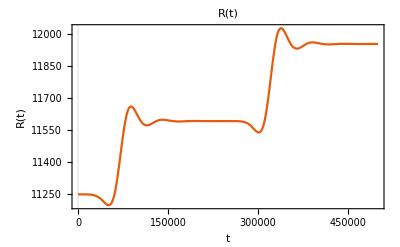

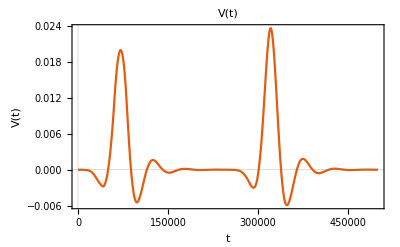

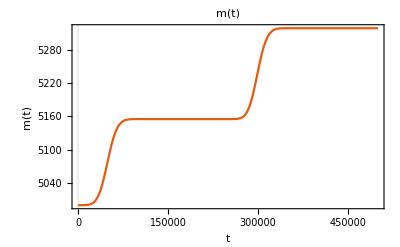

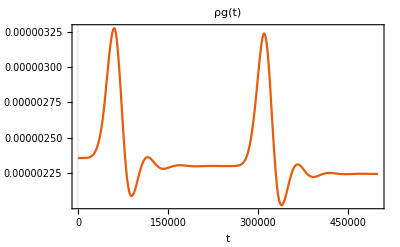

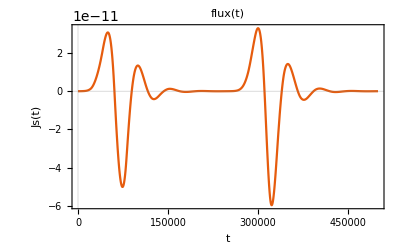

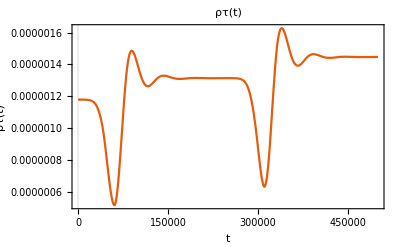

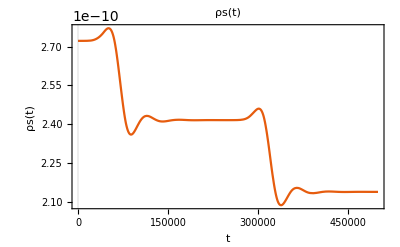

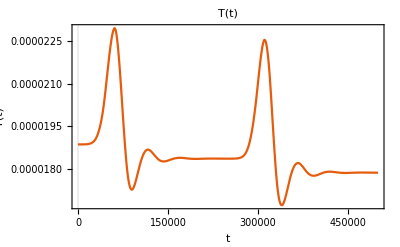

Initial-value Deviations

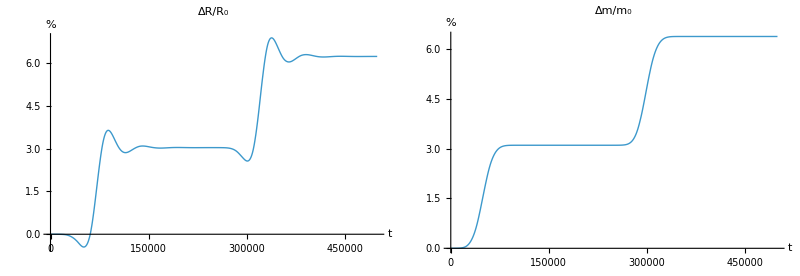

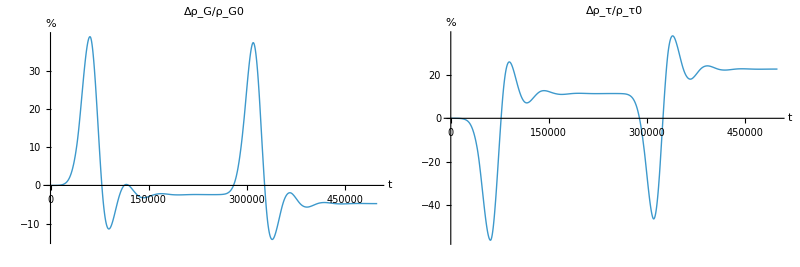

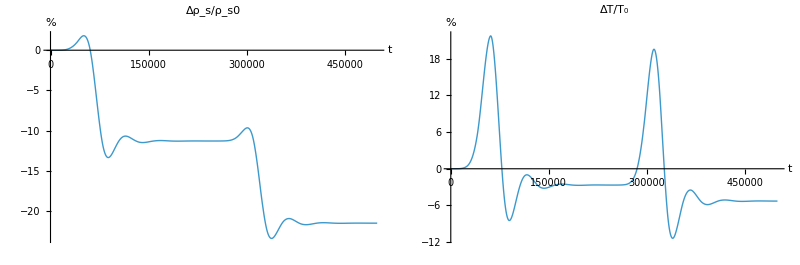

Critical-value Deviations

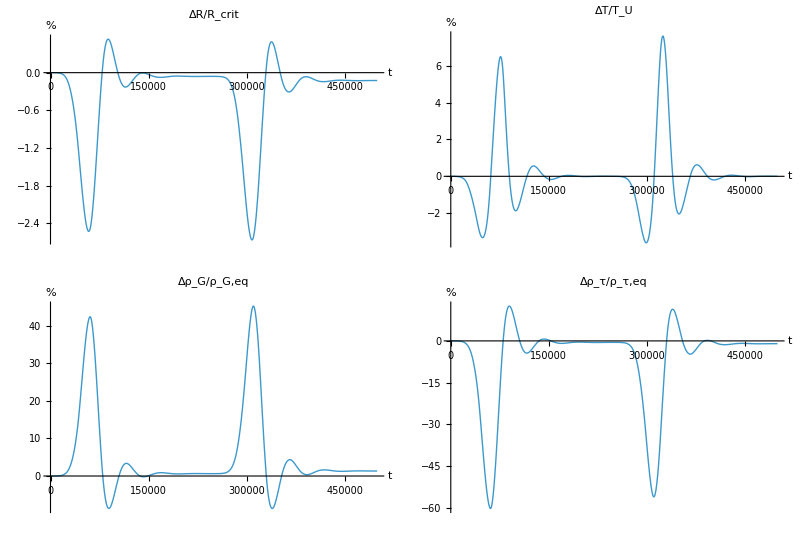

ancillary curves

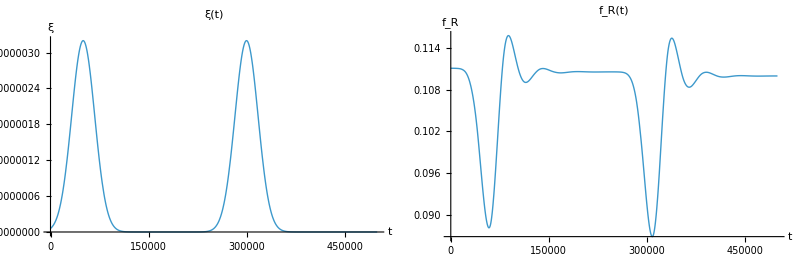

Start of non-linear stability analysis

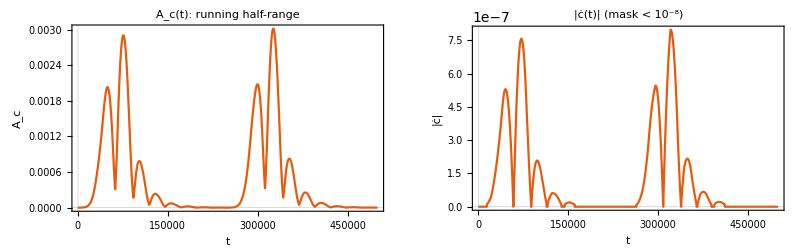

Power-Energy Balance Equation

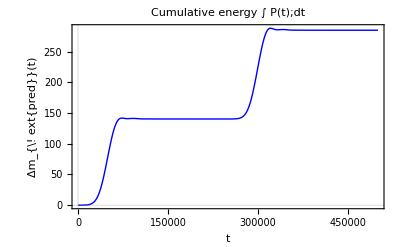

Area  pulse #1 (0 → 150000.)    = 140.29112

Area  pulse #2 (165000. → 500000.) = 144.45082

Total area       (0 → 500000.)        = 284.74194

Δm from m(t): 318.53264   (should match total area-internal heat exchange)

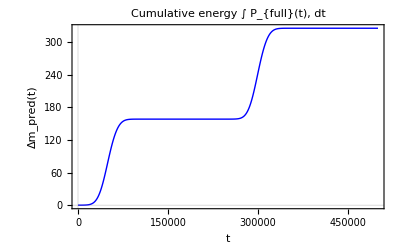

Area  pulse #1 (0 → 150000.)    = 158.55924

Area  pulse #2 (165000. → 500000.) = 167.49319

Total area       (0 → 500000.)        = 326.05243

Δm from m(t): 318.53264   (should match total area)

-Graphics-

Ringdown Analysis

QNM Parameters: τTail0, tMax, ΔτSample, τTailGrid : 450000. | 500000. | 33.3333 |

────────  l = 0  ring-down fit  ────────

Amplitude   A   = 0.54247335

Decay rate  γ   = 0.00004359

Frequency   ω   = 0.00012018

Phase       φ   = 0.31807912

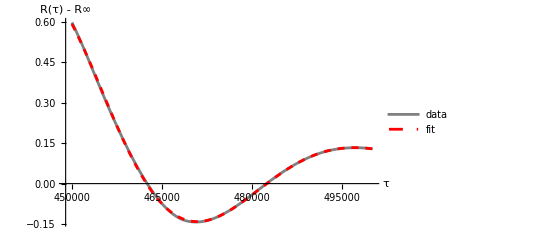

Saved evolution data   →   shellTimeSeries.csv

```mathematica
(*simulation of non-linear dynamics with two kicks: this is the full code to produce the time evolutions of the dynamical variables after an accretion event*)
(*the code also runs a ringdown analysis which, when it converges, will most likely match the linearized frequencies*)
(*the code finally produces a movie showing how the shell reacts to the accretion: this is currently commented out but you can uncomment it*)


ClearAll["Global`*"];

(*---0 ▸ GLOBAL INPUT PARAMETERS-------------------------------------------*)
m0=5000.;
R0=9 m0/4;
k=1/3; (*1/3*)
zeta0=0.1;
tauU=8.*10^-1 m0;  (*8.*10^-1 m0 Excellent for simulation*)
beta=-0.26666; (*-0.26666 -2/5//N*)

alphaFromBetaMass[β_,m_]:=2/3+β-(16 Sqrt[3])/(81 m);
alpha=N@alphaFromBetaMass[beta,m0];

Print["α = ",alpha,"   β = ",beta,"   zeta = ",zeta0,"   tau = ",tauU,"   compactness = ",m0/R0];

(*---0 ▸ EQUILIBRIUM INWARD FLUX ξ0 (kills initial acceleration)--------*)
fR[a_,m_]:=1-2 m/a
fL[a_]:=1+k a^2
aB=R0;
QR0=Sqrt[fR[aB,m0]];
QL0=Sqrt[fL[aB]];
xi0=0 (*Sqrt[(3 k aB QR0+(QL0 QR0-1) (QL0-QR0)/aB)/(8 Pi QL0 aB)]*);
P0star=-((QL0 QR0-1)(QL0-QR0)/R0+3 R0 k QR0)/(16 π QL0 QR0);
Print["ξ₀ = ",ScientificForm[xi0,3]];

(*---1 FLUX PULSE ξ(t)---------------------------------------------------*)
Axi=3.2*10^(-6); (*3.2*10^(-6)*)
tauAxi=10 m0;
sndKick = 6;
sigmaXi=5 m0; (*fixed at 1*)
xiFunc[t_]:=If[t<=0,xi0,Axi (Exp[-((t-tauAxi)/sigmaXi)^2]+Exp[-((t-sndKick tauAxi)/sigmaXi)^2])];   (*ξU=ξS*) (*(Exp[-((τ-τa)/σ)^2]+Exp[-((τ-sndKick τa)/σ)^2])*)

(*---closed-form relation Δm=(4π/3) R0^2 Aξ^2 σ √(π/2)-----------*)
targetFrac=0.02;
deltaM=targetFrac m0;
AxiNeeded=Sqrt[deltaM*3/(4 Pi R0^2 sigmaXi Sqrt[Pi/2])]//N;
Print["For σ = ",sigmaXi/m0," m₀ and Δm/m₀ = ",targetFrac,",   Axi = ",ScientificForm[AxiNeeded,3]];

(*---2 EQUATION-OF-STATE HELPERS-----------------------------------------*)
rhoG[a_,m_]:=(2-3 Sqrt[fR[a,m]])/(12 Pi a);         (*gas*)
rhoS[a_]:=1/(16 Pi Sqrt[k] a^2);                    (*surface*)
rhoTauEv[a_]:=Sqrt[k]/(4 Pi)-1/(6 Pi a)+1/(16 Pi Sqrt[k] a^2);
TU[a_,m_]:=m/(2 Pi a^2 Sqrt[fR[a,m]]);

(*---3 INITIAL CONDITIONS-------------------------------------------------*)
rhoG0=rhoG[R0,m0];
rhoS0=rhoS[R0];
rhoTau0=rhoG0/2+rhoS0-P0star;
T0=TU[R0,m0];

Print["ρG0 = ",ScientificForm[rhoG0,4],"   ρS0 = ",ScientificForm[rhoS0,4],"   ρΤ0 = ",ScientificForm[rhoTau0,4],"   T0 = ",ScientificForm[T0,4],   "   Balancing Pressure = ",ScientificForm[P0star,4]];

(*---4 NUMERICS-----------------------------------------------------------*)
precProd=40;  (*MachinePrecision*)
wpOpts={};
tMax=100 m0;
maxFracStep=.04;
delta=10.^-30;                   (*floor for positives*)

Print["Precision, tMax, first hit, sigma, amplitude: ", precProd,"|", tMax,"|", tauAxi,"|", sigmaXi,"|",Axi]

(*Farea:=2 (V/R-2m V/(R(R-2 m)));*)

(*---5 COMPILED RHS-------------------------------------------------------*)
ClearAll[getRHS];
getRHS=With[{kC=k,alphaC=alpha,betaC=beta,zeta0C=zeta0,tauUC=tauU,deltaC=delta,AxiC=Axi,tauAxiC=tauAxi,sigmaXiC=sigmaXi,xi0C=xi0, sndKickC=sndKick},Compile[{{t,_Real},{y,_Real,1}},Module[{R=y[[1]],V=y[[2]],rhoG=y[[3]],rhoTau=y[[4]],rhoS=y[[5]],T=y[[6]],m=y[[7]],fRloc,qR,qL,dQ,xi,Pnet,Rddot,aR,js,mDot},xi=If[t<=0.,xi0C,AxiC*(Exp[-((t-tauAxiC)/sigmaXiC)^2]+Exp[-((t-sndKickC*tauAxiC)/sigmaXiC)^2])];
fRloc=1-2. m/R;
qR=Sqrt[Max[fRloc+V^2,deltaC]];
qL=Sqrt[1+kC R^2+V^2];
dQ=qL-qR;
Pnet=rhoG/2-rhoTau+rhoS-(2 zeta0C V/R);
Rddot=((3 R kC) qR-4 Pi qL (R (2 xi^2)-4 Pnet qR))/(2 dQ)+(qL qR-1-V^2)/(2 R);
aR=(4 Pi R^2 (2 xi^2)+2 Rddot R+1-fRloc)/(2 qR R);
js=3 rhoG ((alphaC/tauUC) (aR/(2 Pi T)-1)+betaC V/R);
mDot=(4 Pi R^2 qR (qR xi-V xi)^2)/fRloc;
{V,Rddot,-(3 rhoG V/(R)-js-4 zeta0C V^2/R^2-xi^2),-js,-4 rhoS V/R,(aR/(2 Pi)-T)/tauUC,mDot}],RuntimeOptions->"Speed",CompilationTarget->"WVM"]]; (*CompilationTarget->"C"*)

(*---6 SYMBOLIC GUARD-----------------------------------------------------*)
ClearAll[RHS];
RHS[t_?NumericQ,yVec_?VectorQ]:=getRHS[t,yVec];

(*---7 INTEGRATE----------------------------------------------------------*)
initialVec={R0,0.,rhoG0,rhoTau0,rhoS0,T0,m0};

aR0analytic=(4 Pi R0^2 (2 xi0^2)+1-fR[R0,m0])/(2 QR0 R0);
rhs0=getRHS[0.,initialVec];
aR0rhs=2 Pi (rhs0[[6]]*tauU+T0);

Print["Pre-run sanity checks"];
Print["R̈(0) check → ",getRHS[0.,initialVec][[2]]//ScientificForm[#,3]&];
Print["a_R(0) (analytic)  = ",ScientificForm[aR0analytic,6]];
Print["a_R(0) (inside RHS) = ",ScientificForm[aR0rhs,6]];

solY=NDSolveValue[{y'[t]==RHS[t,y[t]],y[0]==initialVec},y,{t,0,tMax},Method->{"StiffnessSwitching","NonstiffTest"->False}(*Method->{"BDF","MaxDifferenceOrder"->5}*),MaxStepFraction->maxFracStep,Evaluate@wpOpts];

(*---8 QUICK CHECK--------------------------------------------------------*)
Print["Δm/m0  =  ",ScientificForm[(solY[tMax][[7]]-m0)/m0,6]];

Print["Evolution of Each State Variable"]

Rsol[t_]:=solY[t][[1]];
Plot[Rsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"R(t)",AxesLabel->{"t","R(t)"},PlotTheme->"Scientific"]
Vsol[t_]:=solY[t][[2]];
Plot[Vsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"V(t)",AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
msol[t_]:=solY[t][[7]];
Plot[msol[t],{t,0,tMax},PlotRange->All,PlotLabel->"m(t)",AxesLabel->{"t","m(t)"},PlotTheme->"Scientific"]
rhoGsol[t_]:=solY[t][[3]];
Plot[rhoGsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρg(t)",AxesLabel->{"t","ρg(t)"},PlotTheme->"Scientific"]
jGas[t_?NumericQ]:=-getRHS[t,solY[t]][[4]];   (*+js*)
Plot[jGas[t],{t,0,tMax},PlotRange->All,PlotLabel->"flux(t)",AxesLabel->{"t","Js(t)"},PlotTheme->"Scientific"]
rhoTausol[t_]:=solY[t][[4]];
Plot[(rhoTausol[t]+P0star),{t,0,tMax},PlotRange->All,PlotLabel->"ρτ(t)",AxesLabel->{"t","ρτ(t)"},PlotTheme->"Scientific"]
rhoSsol[t_]:=solY[t][[5]];
Plot[rhoSsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρs(t)",AxesLabel->{"t","ρs(t)"},PlotTheme->"Scientific"]
Tsol[t_]:=solY[t][[6]];
Plot[Tsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"T(t)",AxesLabel->{"t","T(t)"},PlotTheme->"Scientific"]
aRinst[t_?NumericQ]:=Module[{state=solY[t],rhs=getRHS[t,solY[t]]},2 Pi (rhs[[6]]*tauU+state[[6]])]
Plot[aRinst[t],{t,0,tMax},PlotRange->All,PlotLabel->"aR(t): proper acceleration",AxesLabel->{"t","aR"},PlotTheme->"Scientific"]
parea[t_] := 2 Vsol[t]/Rsol[t]
Plot[parea[t],{t,0,tMax},PlotRange->All,PlotLabel->"Δproper area(t)",AxesLabel->{"t","F(t)"},PlotTheme->"Scientific"]
compactness[t_] := msol[t]/Rsol[t]
Plot[compactness[t],{t,0,tMax},PlotRange->All,PlotLabel->"compactness(t)",AxesLabel->{"t","c(t)"},PlotTheme->"Scientific"]
Pwnet[t_?NumericQ]:=Module[{R=Rsol[t],V=Vsol[t],rhoG=rhoGsol[t],aR=aRinst[t],Tloc=Tsol[t],mloc=msol[t],xi=xiFunc[t],qR},qR=Sqrt[Max[1-2 mloc/R+V^2,delta]];
-8 Pi zeta0 V^2+Pi beta rhoG V^2-(2 Pi alpha/tauU) rhoG (aR/(2 Pi)-Tloc)^2+4 Pi R^2 qR xi^2];
Plot[Pwnet[t],{t,0,tMax},PlotRange->All,PlotLabel->"P(t): injection – dissipation",AxesLabel->{"t","net power"},PlotTheme->"Scientific"]


Δm=msol[tMax]-m0;
scale=1.; (*m0/Δm;*)   (*set to m0/Δm to magnify view*)
gscale = m0/Δm;
perc[f_,f0_]:=100. (f/f0-1);

(*9.2 initial-value deviations*)
Print["Initial-value Deviations"]
pltΔR0=Plot[scale perc[Rsol[t],R0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔm0=Plot[perc[msol[t],m0],{t,0,tMax},PlotRange->All,PlotLabel->"Δm/m₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρG0=Plot[scale perc[rhoGsol[t],rhoG0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρτ0=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTau0+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρs0=Plot[scale perc[rhoSsol[t],rhoS0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_s/ρ_s0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔT0=Plot[scale perc[Tsol[t],T0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T₀",AxesLabel->{"t","%"},PlotStyle->Thick];

GraphicsGrid[{{pltΔR0,pltΔm0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρG0,pltΔρτ0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρs0,pltΔT0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]

(*9.3 critical-value deviations*)
(*instantaneous proper acceleration*)

Rcrit[t_]:=9 msol[t]/4;
TUinst[t_?NumericQ]:=aRinst[t]/(2 Pi); (*TUinst[t_]:=TU[Rsol[t],msol[t]];*)
rhoGcrit[t_]:=rhoG[Rcrit[t],msol[t]];
rhoTauCrit[t_]:=rhoTauEv[Rcrit[t]];

Print["Critical-value Deviations"]
pltΔRcrit=Plot[scale perc[Rsol[t],Rcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R_crit",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔTcrit=Plot[scale perc[Tsol[t],TUinst[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T_U",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρGcrit=Plot[scale perc[rhoGsol[t],rhoGcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G,eq",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρTaucrit=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTauCrit[t]+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ,eq",AxesLabel->{"t","%"},PlotStyle->Thick];

GraphicsGrid[{{pltΔRcrit,pltΔTcrit},{pltΔρGcrit,pltΔρTaucrit},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]

(*9.4 ancillary curves*)
Print["ancillary curves"]
kick[t_]:=xiFunc[t];
fRcheck[t_]:=1-2 msol[t]/Rsol[t];

pltKick=Plot[kick[t],{t,0,tMax},PlotRange->All,PlotLabel->"ξ(t)",AxesLabel->{"t","ξ"},PlotStyle->Thick];
pltfR=Plot[fRcheck[t],{t,0,tMax},PlotRange->All,PlotLabel->"f_R(t)",AxesLabel->{"t","f_R"},PlotStyle->Thick];
GraphicsGrid[{{pltKick,pltfR},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]


(***********Start of non-linear stability analysis**********************************)
Print["Start of non-linear stability analysis"]

dtSample=m0/50.;
tSamples=Range[0.,tMax,dtSample];
cSamples=compactness/@tSamples;

(*derivative and masking*)
cDot=Append[Differences[cSamples]/dtSample,0.];
slopeFrac=1.*10^-8;                (*keep α=0.50 flips visible*)
cleanSlope=If[Abs[#]<slopeFrac,0.,#]&/@cDot;

(*1 monotone-slope test (window 2 τu)*)
winMono=2 tauAxi;
stepsMono=Max[2,Round[winMono/dtSample]];

runs=SplitBy[Transpose[{tSamples,cleanSlope}],Sign[Last[#]]&];
monotoneTimes=Cases[runs,r_List/;(r[[1,2]]!=0.&&Length[r]>=stepsMono):>Mean[r[[All,1]]]];

(*2 envelope test (window 2 τu)*)
winEnv=2 tauU;
stepsEnv=Max[2,Round[winEnv/dtSample]];
halfRange[i_]:=(Max[cSamples[[Max[1,i-stepsEnv+1];;i]]]-Min[cSamples[[Max[1,i-stepsEnv+1];;i]]])/2;
envAmp=Table[halfRange[i],{i,Length[cSamples]}];
epsFrac=0.01;
eps=epsFrac*compactness[0];
unstableEnvelopeTimes=Pick[tSamples,envAmp,_?(#>eps&)];

(*3 ▸ high-frequency sign-flip test (window 1 τAxi)*)
winFlip=2 tauAxi;
stepsFlip=Max[2,Round[winFlip/dtSample]];
crossThr=4;                       (* ≥2 flips per window*)
trailWin=winFlip;

countFlips[v_]:=Module[{nz=DeleteCases[Sign[v],0]},If[Length[nz]<2,0,Count[Partition[nz,2,1],{x_,y_}/;x*y<0]]];
flipCounts=Table[countFlips@Take[cleanSlope,{i,i+stepsFlip-1}],{i,1,Length[cleanSlope]-stepsFlip+1}];
tMidFlip=tSamples[[stepsFlip;;]]-winFlip/2;
flipTimes=Pick[tMidFlip,flipCounts,_?(#>=crossThr&)];
maxFlips=If[flipCounts==={},0,Max[flipCounts]];
avgflips = Mean[flipCounts];
lateFlips=Select[flipTimes,#>=tMax-trailWin&];

(*4 ▸ sustained drift test---*)
devFrac=0.02;                    (*2 % absolute drift*)
devWin=2 tauAxi;                  (*1 τ_Axi persistence window*)
devThr=devFrac*compactness[0];
stepsDev=Max[2,Round[devWin/dtSample]];
driftMaskNum=UnitStep[Abs[cSamples-compactness[0]]-devThr];  (*0/1*)
kernel=ConstantArray[1,stepsDev];
(*one value per complete window*)
driftCounts=ListConvolve[kernel,driftMaskNum,{stepsDev,1},0];
(*centre-time of each window that produced a count*)
tCenterDev=tSamples[[stepsDev;;]]-devWin/2;
(*windows whose count equals the full length->drift all the way*)
driftTimes=Pick[tCenterDev,driftCounts,stepsDev];

(*----------------------------------------------------------diagnostic plots----------------------------------------------------------*)
pltEnv=ListPlot[Transpose[{tSamples,envAmp}],Joined->True,PlotRange->All,PlotLabel->"A_c(t): running half-range",AxesLabel->{"t","A_c"},PlotTheme->"Scientific"];
pltSlope=ListPlot[Transpose[{tSamples,Abs[cleanSlope]}],Joined->True,PlotRange->All,PlotLabel->"|ċ(t)|  (mask < 10⁻⁸)",AxesLabel->{"t","|ċ|"},PlotTheme->"Scientific"];

GraphicsGrid[{{pltEnv,pltSlope}},Spacings->0.8]
(*----------------------------------------------------------verdict----------------------------------------------------------*)
If[monotoneTimes=!={},Print["⚠  Monotone-slope instability begins near t ≈ ",NumberForm[First[monotoneTimes],6]]];
If[unstableEnvelopeTimes=!={},Print["⚠  Envelope never decays below ",NumberForm[eps,6],"  (limit-cycle) up to t ≈ ",NumberForm[Last[unstableEnvelopeTimes],6]]];
If[lateFlips=!={},Print["⚠  Persistent high-frequency oscillations: ",maxFlips," flips per ",NumberForm[winFlip,6],"-unit window; last window centred at t ≈ ",NumberForm[Last[lateFlips],6]]];
If[driftTimes=!={},Print["⚠  Sustained compactness drift |c(t)-c(0)| > ",NumberForm[devThr,6]," for at least one τ_Axi window; last occurrence at t ≈ ",NumberForm[Last[driftTimes],6]]];
If[monotoneTimes==={}&&unstableEnvelopeTimes==={}&&flipTimes==={}&&driftTimes==={},Print["✓  Compactness tests all clear — trajectory non-linearly stable."]];

(**************************************************************************)

(********************Power-Energy Balance Equation***********************************)
Print["Power-Energy Balance Equation"]

dtGrid=m0/50.;    
tGrid=Range[0.,tMax,dtGrid];           (*length N*)
Ps=Pwnet/@tGrid/. Indeterminate->0;
(*-------------------------------------------------------------*)
(*2. Trapezoid areas Δt*.bd (P_i+P_{i+1})*)
(*     ->vector length N-1,same as Differences[tGrid]*)
(*-------------------------------------------------------------*)
stepAreas=Differences[tGrid]*0.5 (Most[Ps]+Rest[Ps]);   
ΔmPred=Prepend[Accumulate[stepAreas],0.];  (*length N*)
(*-------------------------------------------------------------*)
(*3. Plot of the cumulative integral only*)
(*-------------------------------------------------------------*)
cumPlot=ListPlot[Transpose[{tGrid,ΔmPred}],Joined->True,PlotStyle->Directive[Blue,Thick],PlotTheme->"Scientific",PlotRange->All,PlotLabel->"Cumulative energy  ∫ P(t);dt",AxesLabel->{"t","Δm_{\!\text{pred}}(t)"}];
cumPlot   (* ←displays the running integral*)
(*-------------------------------------------------------------*)
(*4. numerical checks*)
(*-------------------------------------------------------------*)
firstPulseEnd=sndKick tauAxi/2.;
secondPulseBeg=1.1 firstPulseEnd;
area1=NIntegrate[Pwnet[t],{t,0,firstPulseEnd},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
area2=NIntegrate[Pwnet[t],{t,secondPulseBeg,tMax},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
areaTot=area1+area2;
Print["Area  pulse #1 (0 → ",firstPulseEnd,")    = ",NumberForm[area1,8]];
Print["Area  pulse #2 (",secondPulseBeg," → ",tMax,") = ",NumberForm[area2,8]];
Print["Total area       (0 → ",tMax,")        = ",NumberForm[areaTot,8]];
Print["Δm from m(t): ",NumberForm[msol[tMax]-m0,8],"   (should match total area-internal heat exchange)"];


extraHeat[t_?NumericQ]:=Module[{V=Vsol[t],rhoG=rhoGsol[t],aR=aRinst[t],T=Tsol[t]},8 Pi zeta0 V^2-Pi beta rhoG V^2+(2 Pi alpha/tauU) rhoG (aR/(2 Pi)-T)^2];
Pfull[t_?NumericQ]:=Pwnet[t]+extraHeat[t];
Ps=Pfull/@tGrid;                 
stepAreas=Differences[tGrid]*0.5 (Most[Ps]+Rest[Ps]);
ΔmPredc=Prepend[Accumulate[stepAreas],0.];
cumPlotc=ListPlot[Transpose[{tGrid,ΔmPredc}],Joined->True,PlotStyle->Directive[Blue,Thick],PlotTheme->"Scientific",PlotRange->All,PlotLabel->"Cumulative energy  ∫ P_{full}(t), dt",AxesLabel->{"t","Δm_pred(t)"}];
cumPlotc   (*shows running integral that should now match m(t)*)
area1=NIntegrate[Pfull[t],{t,0,firstPulseEnd},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
area2=NIntegrate[Pfull[t],{t,secondPulseBeg,tMax},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
areaTot=area1+area2;
Print["Area  pulse #1 (0 → ",firstPulseEnd,")    = ",NumberForm[area1,8]];
Print["Area  pulse #2 (",secondPulseBeg," → ",tMax,") = ",NumberForm[area2,8]];
Print["Total area       (0 → ",tMax,")        = ",NumberForm[areaTot,8]];
Print["Δm from m(t): ",NumberForm[msol[tMax]-m0,8],"   (should match total area)"];

(**********************************************************************************)

(*****************************************************************)

(*instant surface tension*)
σInst[t_?NumericQ]:=σShell[a, adot, addot]/.{a->Rsol[t],adot->Vsol[t],addot->getRHS[t,solY[t]][[2]],M->msol[t],k->k}//N 
(*instantaneous potential along the run*)
Vdyn[t_?NumericQ]:=V[a]/. {a->Rsol[t],v->Vsol[t],σsymb->σInst[t], k->k, M->msol[t]};
(*quick plot*)
ListPlot[Table[{t,σInst[t]},{t,0,tMax,dtGrid}],Joined->True,PlotRange->All,PlotLabel->"Instantaneous V(R) along trajectory",AxesLabel->{"t","V(R(t))"}]


(*******************************************************************)

(*Ringdown Analysis*)
Print["Ringdown Analysis"]

R[t_?NumericQ]:=solY[t][[1]];
Rdot[t_?NumericQ]:=solY[t][[2]];
rhoG[t_?NumericQ]:=solY[t][[3]];
rhoTau[t_?NumericQ]:=solY[t][[4]];
rhoS[t_?NumericQ]:=solY[t][[5]];
Tsol[t_?NumericQ]:=solY[t][[6]];
msol[t_?NumericQ]:=solY[t][[7]];

(*---1 choose a “tail” window,long after the pulse has passed----------*)
τKickEnd=sndKick tauAxi+6 sigmaXi;                (*6 widths after peak*)
τTail0=Max[τKickEnd,0.05 tMax];          (*safety margin*)

ΔτSample=(tMax-τTail0)/1500.;              (* ~800 samples*)
τTailGrid=Range[τTail0,tMax,ΔτSample];
Print["QNM Parameters: τTail0, tMax, ΔτSample, τTailGrid : ",τTail0," | ",tMax," | ",ΔτSample," | "(*,τTailGrid*)]

rTail=R/@τTailGrid;
rInf=Mean[rTail[[-1200;;-1]]];          (*late–time baseline*)
(*Print["Fitted values: rTail ",rTail]*)
(*Print["Fitted values: rInf ",rInf]*)
(*---2 damped–sinusoid fit R(τ)-R∞=A e^{-γ(τ-τ0)} cos[…]+C--------*)

fitModel=A Exp[-γ (τ-τ0)] Cos[ω (τ-τ0)+φ]+C ; (*A Exp[-γ (τ-τ0)] Exp[-ω (τ-τ0)+φ]+C*)
fit=Quiet@FindFit[Transpose[{τTailGrid,rTail}],fitModel,{{A,rTail[[1]]-rInf},{γ,0.01},{ω,0.09},{φ,0},{C,rInf},{τ0,τTail0}},τ,WorkingPrecision->20];
{γFit,ωFit}={γ,ω}/. fit;

Print["\n────────  l = 0  ring-down fit  ────────"];
Print/@{"Amplitude   A   = "<>ToString@NumberForm[A/. fit,{8,8}],"Decay rate  γ   = "<>ToString@NumberForm[γFit,{8,8}],"Frequency   ω   = "<>ToString@NumberForm[ωFit,{8,8}],"Phase       φ   = "<>ToString@NumberForm[φ/. fit,{8,8}]};

(*---3 visual check---*)
Show[ListLinePlot[Transpose[{τTailGrid,rTail-rInf}],PlotStyle->Gray,PlotLegends->{"data"},AxesLabel->{"τ","R(τ) - R∞"}],Plot[Evaluate[fitModel/. fit]-rInf,{τ,τTail0,tMax},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->{"fit"}]]

(*---4 export full time–series------------------------------------------*)
ts=Range[0,tMax,ΔτSample];
data=Table[{τ,R[τ],Rdot[τ],rhoG[τ],(rhoTau[τ]+P0star),rhoS[τ],Tsol[τ],msol[τ]},{τ,ts}];

destq=FileNameJoin[{NotebookDirectory[],"shellTimeSeries.csv"}];
Export[destq,Prepend[data,{"τ","R","Rdot","rho_g","rho_tau","rho_s","T","m"}],"CSV"];

Print["Saved evolution data   →   shellTimeSeries.csv"]

(*End of producing QNMs*)

(*
(*MOVIE–Visualising the accretion pulse*)
Print["Movie-visualisation of the accretion pulse"]

(*---0 ▸ helpers that pull numeric values----------------------------------*)
R[t_?NumericQ]:=N[solY[t][[1]],MachinePrecision];
V[t_?NumericQ]:=N[solY[t][[2]],MachinePrecision];
rhoG[t_?NumericQ]:=N[solY[t][[3]],MachinePrecision];
rhoTau[t_?NumericQ]:=N[solY[t][[4]],MachinePrecision];
rhoS[t_?NumericQ]:=N[solY[t][[5]],MachinePrecision];
Tsol[t_?NumericQ]:=N[solY[t][[6]],MachinePrecision];
msol[t_?NumericQ]:=N[solY[t][[7]],MachinePrecision];

Rcrit[t_?NumericQ]:=9 msol[t]/4;
TUinst[t_?NumericQ]:=aRinst[t]/(2 Pi);(*TU[R[t],msol[t]]*)
rhoGcrit[t_?NumericQ]:=rhoG[Rcrit[t],msol[t]];
rhoTauCrit[t_?NumericQ]:=rhoTauEv[Rcrit[t]];

(*pre-compute an outer scale once (largest R reached)---------------------*)
τsamples=Range[0.,tMax,tMax/100.];
Rmax=1.05 Max[R/@τsamples];     (*5 % padding*)

(*---1 ▸ frame generator---------------------------------------------------*)
Clear[makeFrame]
makeFrame[τ_?NumericQ]:=Module[{Rval,mval,RB,RH,hue,shell,horizon,buchdahl,arrows,bars,gMain,gFull,lbl},Rval=R[τ];mval=msol[τ];
RB=9 mval/4(*Rcrit[τ]*);RH=2 mval;
hue=ColorData["TemperatureMap"]@Rescale[Tsol[τ]/TUinst[τ],{0.2,1.2}];
shell={EdgeForm[{Black,Thick}],hue,Disk[{0,0},Rval]};
horizon={Black,Disk[{0,0},RH]};
buchdahl={Directive[Dashed,Blue,Thick],Circle[{0,0},RB]};
arrows=If[xiFunc[τ]>0,Graphics[{Directive[Arrowheads[Medium],Darker@Red],Arrow[{{1.05 Rmax,0},{0.55 Rmax,0}}]}],Graphics[{}]];
bars=BarChart[{rhoG[τ]/rhoGcrit[τ],(rhoTau[τ]+P0star)/(rhoTauCrit[τ]+P0star)},PlotRange->All(*{-1.0,1.5}*),ChartStyle->{Orange,Purple},ChartLabels->(Style[#,11]&)/@{"ρ_g/ρ_g,eq","ρ_τ/ρ_τ,eq"},Axes->None,ImageSize->{130,130}];
gMain=Graphics[{horizon,shell,buchdahl},PlotRange->All(*{{-Rmax,Rmax},{-Rmax,Rmax}}*),ImageSize->400];
gFull=Overlay[{gMain,arrows,Inset[bars,Scaled[{1,1}],{Left,Center}]}];
lbl=Style[Row[{NumberForm[τ/m0,{5,2}]," m"}],14];
Labeled[Framed[gFull,Background->White,RoundingRadius->15,FrameStyle->None,FrameMargins->Medium],lbl,{Bottom}]]

(*---2 ▸ generate frames---------------------------------------------------*)
τgrid=Subdivide[0.,tMax,799];   (*1000 frames~8 s@30 fps*)

Print["Rendering ",Length[τgrid]," frames …"];
frames=makeFrame/@τgrid;        
(*---3 ▸ export video------------------------------------------------------*)
dest=FileNameJoin[{NotebookDirectory[],"accretion_caseB.mp4"}];
Export[dest,frames,"MP4","FrameRate"->30];
Print["Video saved to: ",dest]*)
```

α = 0.399938   β = -0.26666   zeta = 0.1   tau = 5000.

ξ₀ = 0

For σ = 4. m₀ and Δm/m₀ = 0.002,   Axi = 8.67×10^-7

ρG0 = 2.358×10^-6   ρS0 = 2.723×10^-10   ρΤ0 = 4.594×10^-2   T0 = 1.886×10^-5   Balancing Pressure = -4.594×10^-2

Precision, tMax, first hit, sigma, amplitude: 40|500000.|300000.|20000.|3.×10^-6

Pre-run sanity checks

R̈(0) check → 9.71×10^-17

a_R(0) (analytic)  = 1.18519×10^-4

a_R(0) (inside RHS) = 1.18519×10^-4

Δm/m0  =  2.23316×10^-2

Evolution of Each State Variable

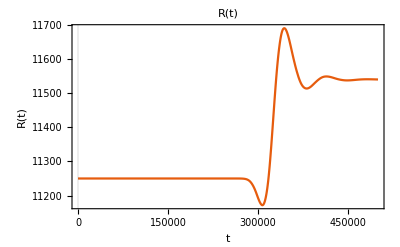

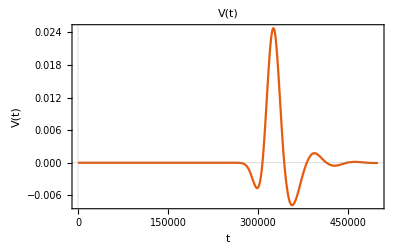

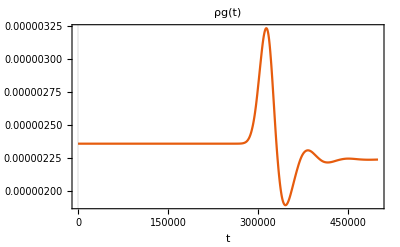

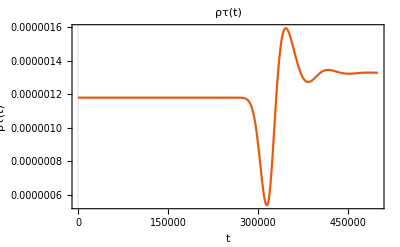

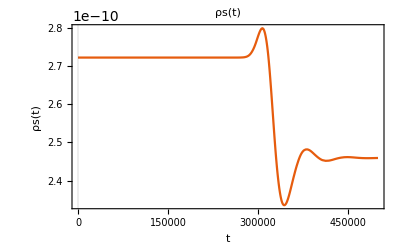

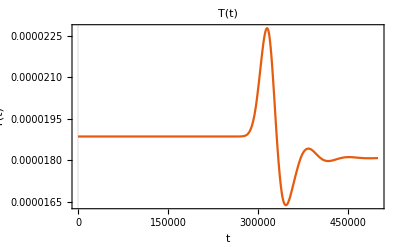

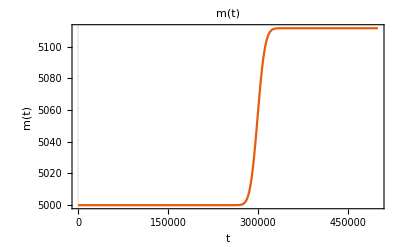

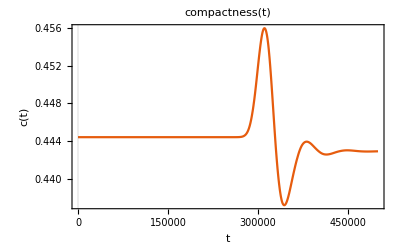

Initial-value Deviations

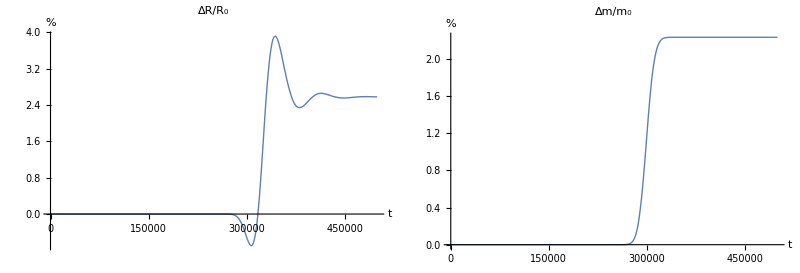

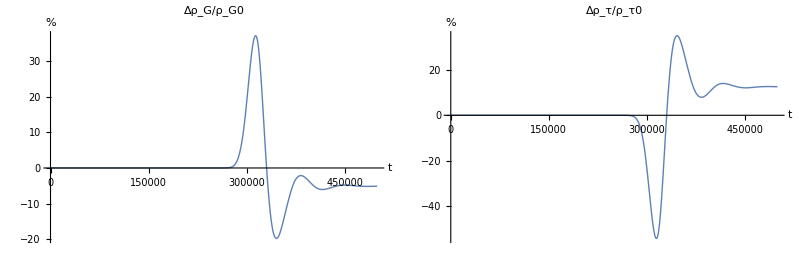

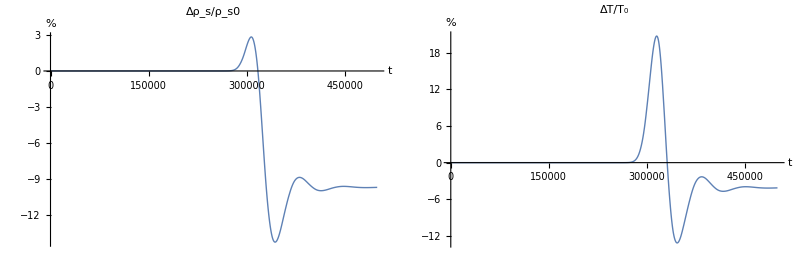

Critical-value Deviations

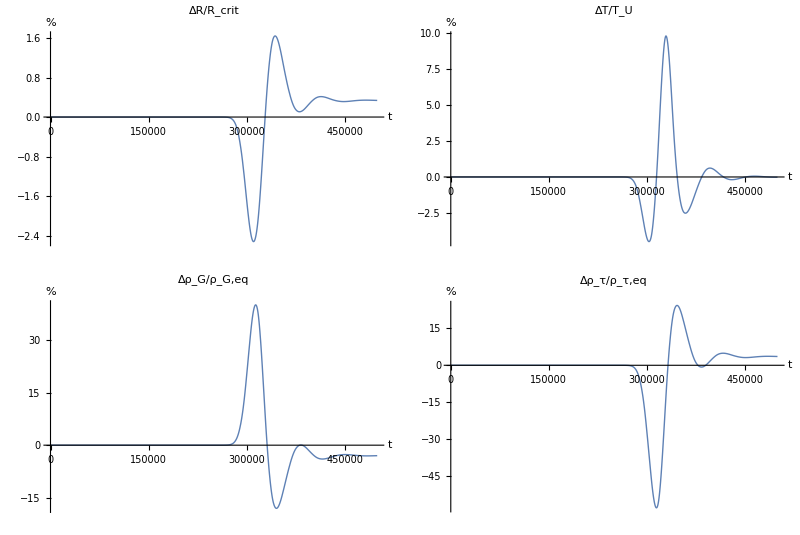

ancillary curves

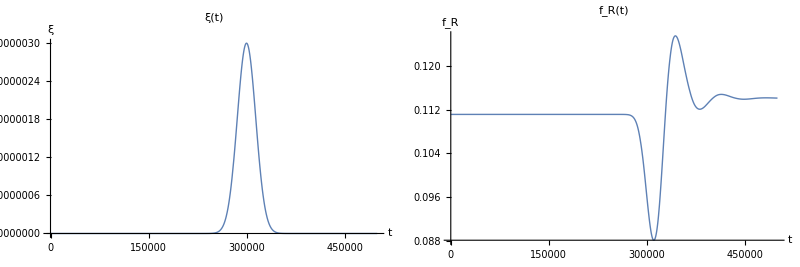

QNM Parameters: τTail0, tMax, ΔτSample, τTailGrid : 420000. | 500000. | 53.3333 |

────────  l = 0  ring-down fit  ────────

Amplitude   A   = 7.57494100

Decay rate  γ   = 0.00003606

Frequency   ω   = 0.00009224

Phase       φ   = 6.44828600

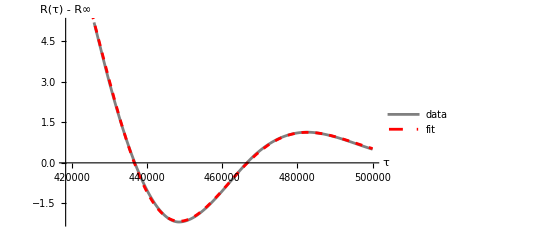

Saved evolution data   →   shellTimeSeries.csv

```mathematica
(*One late-time kick with better simulation of the ringdown*)

ClearAll["Global`*"];

(*---0 GLOBAL INPUT PARAMETERS-------------------------------------------*)
m0=5000.;
R0=9 m0/4;
k=1/3;
zeta0=0.1;
tauU=10.*10^-1 m0;  (*8.*10^-1 m0 Excellent for simulation to show the return to *)
beta=-0.26666;

alphaFromBetaMass[β_,m_]:=2/3+β-(16 Sqrt[3])/(81 m);
alpha=N@alphaFromBetaMass[beta,m0];

Print["α = ",alpha,"   β = ",beta,"   zeta = ",zeta0,"   tau = ",tauU];

(*---0a ▸ EQUILIBRIUM INWARD FLUX ξ0 (kills initial acceleration)--------*)
fR[a_,m_]:=1-2 m/a
fL[a_]:=1+k a^2
aB=R0;
QR0=Sqrt[fR[aB,m0]];
QL0=Sqrt[fL[aB]];
xi0=0 (*Sqrt[(3 k aB QR0+(QL0 QR0-1) (QL0-QR0)/aB)/(8 Pi QL0 aB)]*);
P0star=-((QL0 QR0-1)(QL0-QR0)/R0+3 R0 k QR0)/(16 π QL0 QR0);
Print["ξ₀ = ",ScientificForm[xi0,3]];

(*---1 ▸ FLUX PULSE ξ(t)---------------------------------------------------*)
Axi=3.*10^(-6);(*1.73*10^(-6)*)(*5.5*10^-7*)
tauAxi=60 m0;
sigmaXi=4 m0; (*fixed at 1*)
xiFunc[t_]:=If[t<=0,xi0,Axi Exp[-((t-tauAxi)/sigmaXi)^2]];   (*ξU=ξS*)

(*---closed-form relation Δm=(4π/3) R0^2 Aξ^2 σ √(π/2)-----------*)
targetFrac=0.002;
deltaM=targetFrac m0;
AxiNeeded=Sqrt[deltaM*3/(4 Pi R0^2 sigmaXi Sqrt[Pi/2])]//N;
Print["For σ = ",sigmaXi/m0," m₀ and Δm/m₀ = ",targetFrac,",   Axi = ",ScientificForm[AxiNeeded,3]];

(*---2 ▸ EQUATION-OF-STATE HELPERS-----------------------------------------*)
rhoG[a_,m_]:=(2-3 Sqrt[fR[a,m]])/(12 Pi a);         (*gas*)
rhoS[a_]:=1/(16 Pi Sqrt[k] a^2);                    (*surface*)
rhoTauEv[a_]:=Sqrt[k]/(4 Pi)-1/(6 Pi a)+1/(16 Pi Sqrt[k] a^2);
TU[a_,m_]:=m/(2 Pi a^2 Sqrt[fR[a,m]]);

(*---3 ▸ INITIAL CONDITIONS-------------------------------------------------*)
rhoG0=rhoG[R0,m0];
rhoS0=rhoS[R0];
rhoTau0=rhoG0/2+rhoS0-P0star;
T0=TU[R0,m0];

Print["ρG0 = ",ScientificForm[rhoG0,4],"   ρS0 = ",ScientificForm[rhoS0,4],"   ρΤ0 = ",ScientificForm[rhoTau0,4],"   T0 = ",ScientificForm[T0,4],   "   Balancing Pressure = ",ScientificForm[P0star,4]];

(*---4 ▸ NUMERICS-----------------------------------------------------------*)
precProd=40;  (*MachinePrecision*)
wpOpts={};
tMax=100 m0;
maxFracStep=.04;
delta=10.^-30;                   (*floor for positives*)

Print["Precision, tMax, first hit, sigma, amplitude: ", precProd,"|", tMax,"|", tauAxi,"|", sigmaXi,"|",Axi]

(*Farea:=2 (V/R-2m V/(R(R-2 m)));*)

(*---5 ▸ COMPILED RHS-------------------------------------------------------*)
ClearAll[getRHS];
getRHS=With[{kC=k,alphaC=alpha,betaC=beta,zeta0C=zeta0,tauUC=tauU,deltaC=delta,AxiC=Axi,tauAxiC=tauAxi,sigmaXiC=sigmaXi,xi0C=xi0},Compile[{{t,_Real},{y,_Real,1}},Module[{R=y[[1]],V=y[[2]],rhoG=y[[3]],rhoTau=y[[4]],rhoS=y[[5]],T=y[[6]],m=y[[7]],fRloc,qR,qL,dQ,xi,Pnet,Rddot,aR,js,mDot},xi=If[t<=0.,xi0C,AxiC*Exp[-((t-tauAxiC)/sigmaXiC)^2]];
fRloc=1-2. m/R;
qR=Sqrt[Max[fRloc+V^2,deltaC]];
qL=Sqrt[1+kC R^2+V^2];
dQ=qL-qR;
Pnet=rhoG/2-rhoTau+rhoS-(2 zeta0C V/R);
Rddot=((3 R kC) qR-4 Pi qL (R (2 xi^2)-4 Pnet qR))/(2 dQ)+(qL qR-1-V^2)/(2 R);
aR=(4 Pi R^2 (2 xi^2)+2 Rddot R+1-fRloc)/(2 qR R);
js=3 rhoG ((alphaC/tauUC) (aR/(2 Pi T)-1)+betaC V/R);
mDot=(4 Pi R^2 qR (qR xi-V xi)^2)/fRloc;
{V,Rddot,-(3 rhoG V/(R)-js-4 zeta0C V^2/R^2-xi^2),-js,-4 rhoS V/R,(aR/(2 Pi)-T)/tauUC,mDot}],RuntimeOptions->"Speed",CompilationTarget->"WVM"]]; (*CompilationTarget->"C"*)

(*---6 ▸ SYMBOLIC GUARD-----------------------------------------------------*)
ClearAll[RHS];
RHS[t_?NumericQ,yVec_?VectorQ]:=getRHS[t,yVec];

(*---7 ▸ INTEGRATE----------------------------------------------------------*)
initialVec={R0,0.,rhoG0,rhoTau0,rhoS0,T0,m0};

aR0analytic=(4 Pi R0^2 (2 xi0^2)+1-fR[R0,m0])/(2 QR0 R0);
rhs0=getRHS[0.,initialVec];
aR0rhs=2 Pi (rhs0[[6]]*tauU+T0);

Print["Pre-run sanity checks"];
Print["R̈(0) check → ",getRHS[0.,initialVec][[2]]//ScientificForm[#,3]&];
Print["a_R(0) (analytic)  = ",ScientificForm[aR0analytic,6]];
Print["a_R(0) (inside RHS) = ",ScientificForm[aR0rhs,6]];

solY=NDSolveValue[{y'[t]==RHS[t,y[t]],y[0]==initialVec},y,{t,0,tMax},Method->{"StiffnessSwitching","NonstiffTest"->False}(*Method->{"BDF","MaxDifferenceOrder"->5}*),MaxStepFraction->maxFracStep,Evaluate@wpOpts];

(*---8 ▸ QUICK CHECK--------------------------------------------------------*)
Print["Δm/m0  =  ",ScientificForm[(solY[tMax][[7]]-m0)/m0,6]];

Print["Evolution of Each State Variable"]
Rsol[t_]:=solY[t][[1]];
Plot[Rsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"R(t)",AxesLabel->{"t","R(t)"},PlotTheme->"Scientific"]
Vsol[t_]:=solY[t][[2]];
Plot[Vsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"V(t)",AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
rhoGsol[t_]:=solY[t][[3]];
Plot[rhoGsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρg(t)",AxesLabel->{"t","ρg(t)"},PlotTheme->"Scientific"]
rhoTausol[t_]:=solY[t][[4]];
Plot[(rhoTausol[t]+P0star),{t,0,tMax},PlotRange->All,PlotLabel->"ρτ(t)",AxesLabel->{"t","ρτ(t)"},PlotTheme->"Scientific"]
rhoSsol[t_]:=solY[t][[5]];
Plot[rhoSsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρs(t)",AxesLabel->{"t","ρs(t)"},PlotTheme->"Scientific"]
Tsol[t_]:=solY[t][[6]];
Plot[Tsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"T(t)",AxesLabel->{"t","T(t)"},PlotTheme->"Scientific"]
msol[t_]:=solY[t][[7]];
Plot[msol[t],{t,0,tMax},PlotRange->All,PlotLabel->"m(t)",AxesLabel->{"t","m(t)"},PlotTheme->"Scientific"]
compactness[t_] := msol[t]/Rsol[t]
Plot[compactness[t],{t,0,tMax},PlotRange->All,PlotLabel->"compactness(t)",AxesLabel->{"t","c(t)"},PlotTheme->"Scientific"]
parea[t_] := 2 Vsol[t]/Rsol[t]
Plot[parea[t],{t,0,tMax},PlotRange->All,PlotLabel->"Δproper area(t)",AxesLabel->{"t","F(t)"},PlotTheme->"Scientific"]


Δm=msol[tMax]-m0;
scale=1.; (*m0/Δm;*)   (*set to m0/Δm to magnify view*)
gscale = m0/Δm;
perc[f_,f0_]:=100. (f/f0-1);

(*9.2 initial-value deviations*)
Print["Initial-value Deviations"]
pltΔR0=Plot[scale perc[Rsol[t],R0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔm0=Plot[perc[msol[t],m0],{t,0,tMax},PlotRange->All,PlotLabel->"Δm/m₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρG0=Plot[scale perc[rhoGsol[t],rhoG0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρτ0=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTau0+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρs0=Plot[scale perc[rhoSsol[t],rhoS0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_s/ρ_s0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔT0=Plot[scale perc[Tsol[t],T0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T₀",AxesLabel->{"t","%"},PlotStyle->Thick];

GraphicsGrid[{{pltΔR0,pltΔm0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρG0,pltΔρτ0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρs0,pltΔT0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]


(*9.3 critical-value deviations*)
(*instantaneous proper acceleration*)

aRinst[t_?NumericQ]:=Module[{state=solY[t],rhs=getRHS[t,solY[t]]},2 Pi (rhs[[6]]*tauU+state[[6]])          (* =2π[(a_R/2π−T)τ_U+T]*)]

Rcrit[t_]:=9 msol[t]/4;
TUinst[t_?NumericQ]:=aRinst[t]/(2 Pi); (*TUinst[t_]:=TU[Rsol[t],msol[t]];*)
rhoGcrit[t_]:=rhoG[Rcrit[t],msol[t]];
rhoTauCrit[t_]:=rhoTauEv[Rcrit[t]];

Print["Critical-value Deviations"]
pltΔRcrit=Plot[scale perc[Rsol[t],Rcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R_crit",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔTcrit=Plot[scale perc[Tsol[t],TUinst[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T_U",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρGcrit=Plot[scale perc[rhoGsol[t],rhoGcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G,eq",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρTaucrit=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTauCrit[t]+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ,eq",AxesLabel->{"t","%"},PlotStyle->Thick];

GraphicsGrid[{{pltΔRcrit,pltΔTcrit},{pltΔρGcrit,pltΔρTaucrit},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]

(*9.4 ancillary curves*)
Print["ancillary curves"]
kick[t_]:=xiFunc[t];
fRcheck[t_]:=1-2 msol[t]/Rsol[t];

pltKick=Plot[kick[t],{t,0,tMax},PlotRange->All,PlotLabel->"ξ(t)",AxesLabel->{"t","ξ"},PlotStyle->Thick];
pltfR=Plot[fRcheck[t],{t,0,tMax},PlotRange->All,PlotLabel->"f_R(t)",AxesLabel->{"t","f_R"},PlotStyle->Thick];
GraphicsGrid[{{pltKick,pltfR},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]

(*Ringdown Analysis*)(*===========================================================================*)
R[t_?NumericQ]:=solY[t][[1]];
Rdot[t_?NumericQ]:=solY[t][[2]];
rhoG[t_?NumericQ]:=solY[t][[3]];
rhoTau[t_?NumericQ]:=solY[t][[4]];
rhoS[t_?NumericQ]:=solY[t][[5]];
Tsol[t_?NumericQ]:=solY[t][[6]];
msol[t_?NumericQ]:=solY[t][[7]];

(*---1 ▸ choose a “tail” window,long after the pulse has passed----------*)
τKickEnd=tauAxi+6 sigmaXi;                (*6 widths after peak*)
τTail0=Max[τKickEnd,0.05 tMax];          (*safety margin*)

ΔτSample=(tMax-τTail0)/1500.;              (* ~800 samples*)
τTailGrid=Range[τTail0,tMax,ΔτSample];
Print["QNM Parameters: τTail0, tMax, ΔτSample, τTailGrid : ",τTail0," | ",tMax," | ",ΔτSample," | "(*,τTailGrid*)]

rTail=R/@τTailGrid;
rInf=Mean[rTail[[-1000;;-1]]];          (*late–time baseline*)
(*Print["Fitted values: rTail ",rTail]*)
(*Print["Fitted values: rInf ",rInf]*)


(*---2 ▸ damped–sinusoid fit R(τ)-R∞=A e^{-γ(τ-τ0)} cos[…]+C--------*)

fitModel=A Exp[-γ (τ-τ0)] Cos[ω (τ-τ0)+φ]+C ; (*A Exp[-γ (τ-τ0)] Exp[-ω (τ-τ0)+φ]+C*)
fit=Quiet@FindFit[Transpose[{τTailGrid,rTail}],fitModel,{{A,rTail[[1]]-rInf},{γ,0.01},{ω,0.09},{φ,0},{C,rInf},{τ0,τTail0}},τ,WorkingPrecision->20];
{γFit,ωFit}={γ,ω}/. fit;

Print["\n────────  l = 0  ring-down fit  ────────"];
Print/@{"Amplitude   A   = "<>ToString@NumberForm[A/. fit,{8,8}],"Decay rate  γ   = "<>ToString@NumberForm[γFit,{8,8}],"Frequency   ω   = "<>ToString@NumberForm[ωFit,{8,8}],"Phase       φ   = "<>ToString@NumberForm[φ/. fit,{8,8}]};

(*---3 ▸ visual check------------------------------------------------------*)
Show[ListLinePlot[Transpose[{τTailGrid,rTail-rInf}],PlotStyle->Gray,PlotLegends->{"data"},AxesLabel->{"τ","R(τ) - R∞"}],Plot[Evaluate[fitModel/. fit]-rInf,{τ,τTail0,tMax},PlotStyle->{Red,Dashed},PlotLegends->{"fit"}]]

(*---4 ▸ export full time–series------------------------------------------*)
ts=Range[0,tMax,ΔτSample];
data=Table[{τ,R[τ],Rdot[τ],rhoG[τ],(rhoTau[τ]+P0star),rhoS[τ],Tsol[τ],msol[τ]},{τ,ts}];

destq=FileNameJoin[{NotebookDirectory[],"shellTimeSeries.csv"}];
Export[destq,Prepend[data,{"τ","R","Rdot","rho_g","rho_tau","rho_s","T","m"}],"CSV"];

Print["Saved evolution data   →   shellTimeSeries.csv"]
(*===========================================================================*)

(*End of producing QNMs*)

(*
(*MOVIE–Visualising the accretion pulse*)
(*---0 ▸ helpers that pull numeric values----------------------------------*)
R[t_?NumericQ]:=N[solY[t][[1]],MachinePrecision];
V[t_?NumericQ]:=N[solY[t][[2]],MachinePrecision];
rhoG[t_?NumericQ]:=N[solY[t][[3]],MachinePrecision];
rhoTau[t_?NumericQ]:=N[solY[t][[4]],MachinePrecision];
rhoS[t_?NumericQ]:=N[solY[t][[5]],MachinePrecision];
Tsol[t_?NumericQ]:=N[solY[t][[6]],MachinePrecision];
msol[t_?NumericQ]:=N[solY[t][[7]],MachinePrecision];

Rcrit[t_?NumericQ]:=9 msol[t]/4;
TUinst[t_?NumericQ]:=aRinst[t]/(2 Pi);(*TU[R[t],msol[t]]*)
rhoGcrit[t_?NumericQ]:=rhoG[Rcrit[t],msol[t]];
rhoTauCrit[t_?NumericQ]:=rhoTauEv[Rcrit[t]];

(* test graphs
Plot[(rhoTau[t]+P0star),{t,0,tMax},PlotRange->All,AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
Plot[(rhoTauCrit[t]+P0star),{t,0,tMax},PlotRange->All,AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
Plot[(rhoTau[t]+P0star)/(rhoTauCrit[t]+P0star),{t,0,tMax},PlotRange->All,AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
*)

(*pre-compute an outer scale once (largest R reached)---------------------*)
τsamples=Range[0.,tMax,tMax/100.];
Rmax=1.05 Max[R/@τsamples];     (*5 % padding*)

(*---1 ▸ frame generator---------------------------------------------------*)
Clear[makeFrame]
makeFrame[τ_?NumericQ]:=Module[{Rval,mval,RB,RH,hue,shell,horizon,buchdahl,arrows,bars,gMain,gFull,lbl},Rval=R[τ];mval=msol[τ];
RB=9 mval/4(*Rcrit[τ]*);RH=2 mval;
hue=ColorData["TemperatureMap"]@Rescale[Tsol[τ]/TUinst[τ],{0.2,1.2}];
shell={EdgeForm[{Black,Thick}],hue,Disk[{0,0},Rval]};
horizon={Black,Disk[{0,0},RH]};
buchdahl={Directive[Dashed,Blue,Thick],Circle[{0,0},RB]};
arrows=If[xiFunc[τ]>0,Graphics[{Directive[Arrowheads[Medium],Darker@Red],Arrow[{{1.05 Rmax,0},{0.55 Rmax,0}}]}],Graphics[{}]];
bars=BarChart[{rhoG[τ]/rhoGcrit[τ],(rhoTau[τ]+P0star)/(rhoTauCrit[τ]+P0star)},PlotRange->All(*{-1.0,1.5}*),ChartStyle->{Orange,Purple},ChartLabels->(Style[#,11]&)/@{"ρ_g/ρ_g,eq","ρ_τ/ρ_τ,eq"},Axes->None,ImageSize->{160,180}];
gMain=Graphics[{horizon,shell,buchdahl},PlotRange->{{-Rmax,Rmax},{-Rmax,Rmax}},ImageSize->400];
gFull=Overlay[{gMain,arrows,Inset[bars,Scaled[{0.5,1}],{Left,Center}]}];
lbl=Style[Row[{NumberForm[τ/m0,{5,2}]," m"}],14];
Labeled[Framed[gFull,Background->White,RoundingRadius->15,FrameStyle->None,FrameMargins->Medium],lbl,{Bottom}]]

(*---2 ▸ generate frames---------------------------------------------------*)
τgrid=Subdivide[0.,tMax,799];   (*1000 frames~8 s@30 fps*)

Print["Rendering ",Length[τgrid]," frames …"];
frames=makeFrame/@τgrid;        
(*---3 ▸ export video------------------------------------------------------*)
dest=FileNameJoin[{NotebookDirectory[],"accretion_caseB.mp4"}];
Export[dest,frames,"MP4","FrameRate"->30];
Print["Video saved to: ",dest]*)
```

α = 4/15   β = -2/5   zeta = 1.   tau = 4000.   compactness = 0.444444

ξ₀ = 0

For σ = 5. m₀ and Δm/m₀ = 0.02,   Axi = 2.45×10^-6

ρG0 = 2.358×10^-6   ρS0 = 2.723×10^-10   ρΤ0 = 4.594×10^-2   T0 = 1.886×10^-5   Balancing Pressure = -4.594×10^-2

Precision, tMax, first hit, second hit, sigma, amplitude: 40|500000.|50000.|300000.|25000.|3.2×10^-6

Pre-run sanity checks

R̈(0) check → 9.71×10^-17

a_R(0) (analytic)  = 1.18519×10^-4

a_R(0) (inside RHS) = 1.18519×10^-4

Pulse times = {5.×10^4,3.×10^5}

Δm/m0  =  5.7299×10^-2

Evolution of Each State Variable

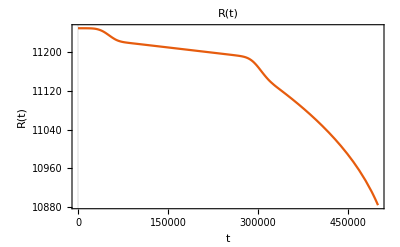

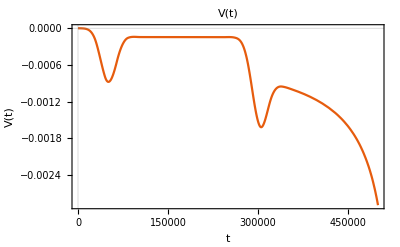

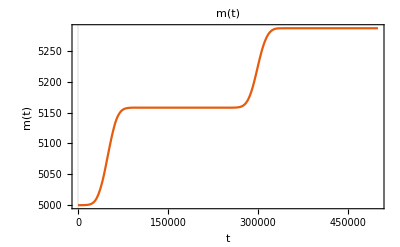

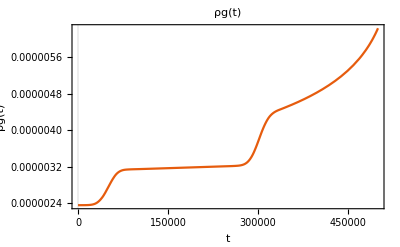

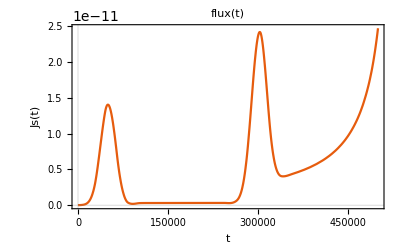

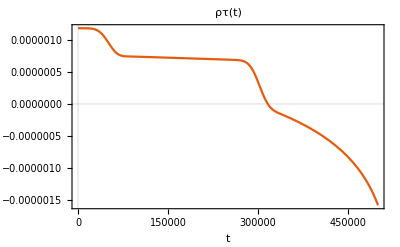

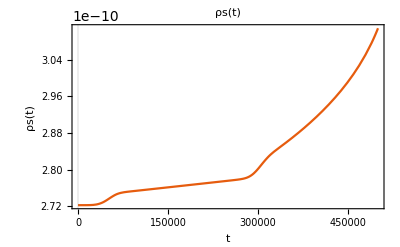

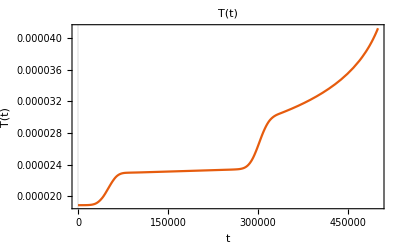

Initial-value Deviations

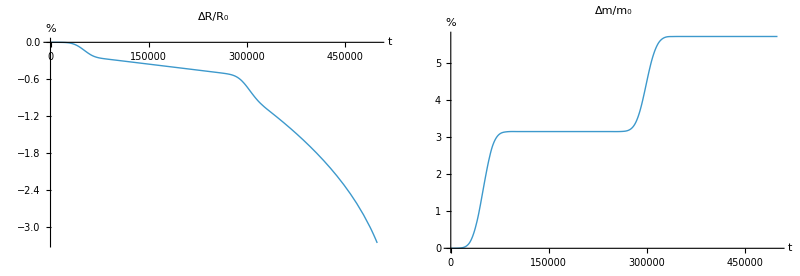

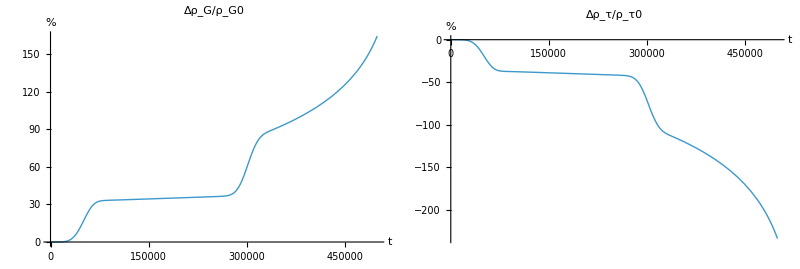

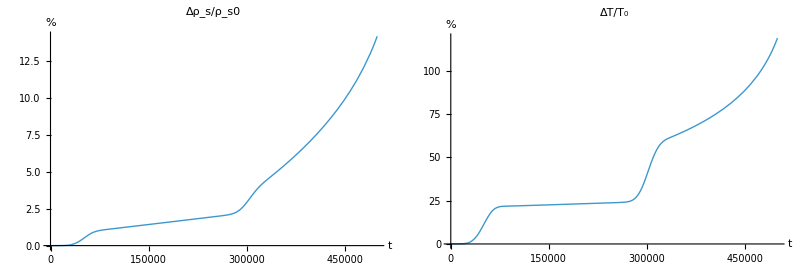

Critical-value Deviations

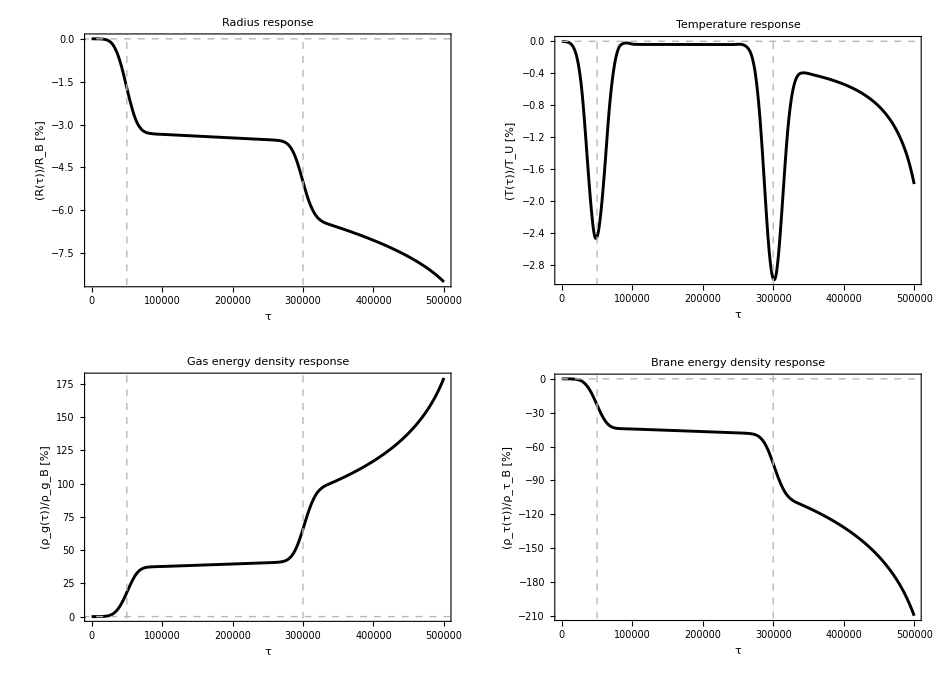

ancillary curves

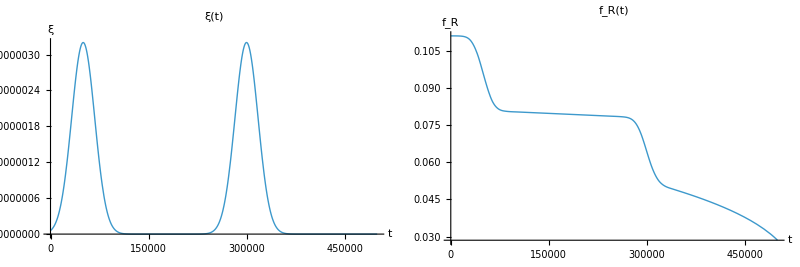

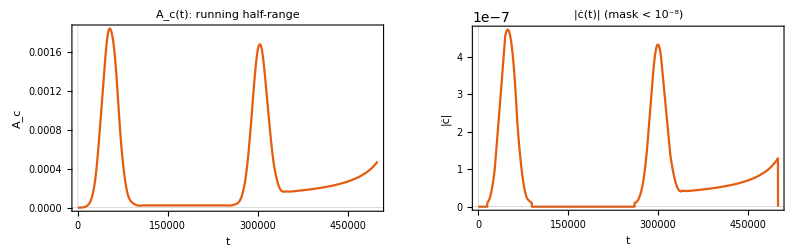

⚠  Monotone-slope instability begins near t ≈ 380300.

⚠  Sustained compactness drift |c(t)-c(0)| > 0.00888889 for at least one τ_Axi window; last occurrence at t ≈ 450000.

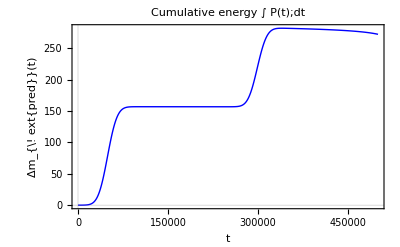

Area  pulse #1 (0 → 150000.)    = 156.75627

Area  pulse #2 (165000. → 500000.) = 115.36144

Total area       (0 → 500000.)        = 272.11772

Δm from m(t): 286.49517   (should match total area-internal heat exchange)

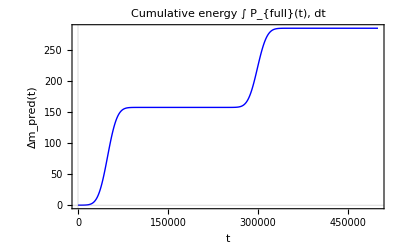

Area  pulse #1 (0 → 150000.)    = 157.26153

Area  pulse #2 (165000. → 500000.) = 127.34923

Total area       (0 → 500000.)        = 284.61076

Δm from m(t): 286.49517   (should match total area)

```mathematica
(*simulation of non-linear dynamics with two kicks but no ringdown or movie*)
ClearAll["Global`*"];

(*---0 ▸ GLOBAL INPUT PARAMETERS-------------------------------------------*)
m0=5000.;
R0=9 m0/4;
k=1/3;
zeta0=1.0;
tauU=8.*10^-1 m0;  (*8.*10^-1 m0 Excellent for simulation*)
beta=-2/5; (*-2/5 from the 2021 paper reexamining slow rotation or -0.2666*)

alphaFromBetaMass[β_,m_]:=2/3+β-(16 Sqrt[3])/(81 m);
alpha=4/15 (*N@alphaFromBetaMass[beta,m0]*); 
(*(*0.266667 or 4/15 from the 2021 paper reexamining slow rotation*), 0.3 gives full convergence*)

Print["α = ",alpha,"   β = ",beta,"   zeta = ",zeta0,"   tau = ",tauU,"   compactness = ",m0/R0];

(*---0a ▸ EQUILIBRIUM INWARD FLUX ξ0 (kills initial acceleration)--------*)
fR[a_,m_]:=1-2 m/a
fL[a_]:=1+k a^2
aB=R0;
QR0=Sqrt[fR[aB,m0]];
QL0=Sqrt[fL[aB]];
xi0=0 (*Sqrt[(3 k aB QR0+(QL0 QR0-1) (QL0-QR0)/aB)/(8 Pi QL0 aB)]*);
P0star=-((QL0 QR0-1)(QL0-QR0)/R0+3 R0 k QR0)/(16 π QL0 QR0);
Print["ξ₀ = ",ScientificForm[xi0,3]];

(*---1 ▸ FLUX PULSE ξ(t)---------------------------------------------------*)
Axi=3.2*10^(-6);(*1.73*10^(-6)*)(*5.5*10^-7*) (*2.74*10^(-6) to go with sigmaXi = 4m*)
tauAxi=10 m0;
sndKick = 6;
sigmaXi=5 m0; (*fixed at 1*)
xiFunc[t_]:=If[t<=0,xi0,Axi (Exp[-((t-tauAxi)/sigmaXi)^2]+Exp[-((t-sndKick tauAxi)/sigmaXi)^2])];   (*ξU=ξS*) (*(Exp[-((τ-τa)/σ)^2]+Exp[-((τ-sndKick τa)/σ)^2])*)

(*---closed-form relation Δm=(4π/3) R0^2 Aξ^2 σ √(π/2)-----------*)
targetFrac=0.02;
deltaM=targetFrac m0;
AxiNeeded=Sqrt[deltaM*3/(4 Pi R0^2 sigmaXi Sqrt[Pi/2])]//N;
Print["For σ = ",sigmaXi/m0," m₀ and Δm/m₀ = ",targetFrac,",   Axi = ",ScientificForm[AxiNeeded,3]];

(*---2 ▸ EQUATION-OF-STATE HELPERS-----------------------------------------*)
rhoG[a_,m_]:=(2-3 Sqrt[fR[a,m]])/(12 Pi a);         (*gas*)
rhoS[a_]:=1/(16 Pi Sqrt[k] a^2);                    (*surface*)
rhoTauEv[a_]:=Sqrt[k]/(4 Pi)-1/(6 Pi a)+1/(16 Pi Sqrt[k] a^2);
TU[a_,m_]:=m/(2 Pi a^2 Sqrt[fR[a,m]]);

(*---3 ▸ INITIAL CONDITIONS-------------------------------------------------*)
rhoG0=rhoG[R0,m0];
rhoS0=rhoS[R0];
rhoTau0=rhoG0/2+rhoS0-P0star;
T0=TU[R0,m0];

Print["ρG0 = ",ScientificForm[rhoG0,4],"   ρS0 = ",ScientificForm[rhoS0,4],"   ρΤ0 = ",ScientificForm[rhoTau0,4],"   T0 = ",ScientificForm[T0,4],   "   Balancing Pressure = ",ScientificForm[P0star,4]];

(*---4 ▸ NUMERICS-----------------------------------------------------------*)
precProd=40;  (*MachinePrecision*)
wpOpts={};
tMax=100 m0;
maxFracStep=.04;
delta=10.^-30;                   (*floor for positives*)

Print["Precision, tMax, first hit, second hit, sigma, amplitude: ", precProd,"|", tMax,"|", tauAxi,"|",sndKick*tauAxi,"|", sigmaXi,"|",Axi]

(*Farea:=2 (V/R-2m V/(R(R-2 m)));*)

(*---5 ▸ COMPILED RHS-------------------------------------------------------*)
ClearAll[getRHS];
getRHS=With[{kC=k,alphaC=alpha,betaC=beta,zeta0C=zeta0,tauUC=tauU,deltaC=delta,AxiC=Axi,tauAxiC=tauAxi,sigmaXiC=sigmaXi,xi0C=xi0, sndKickC=sndKick},Compile[{{t,_Real},{y,_Real,1}},Module[{R=y[[1]],V=y[[2]],rhoG=y[[3]],rhoTau=y[[4]],rhoS=y[[5]],T=y[[6]],m=y[[7]],fRloc,qR,qL,dQ,xi,Pnet,Rddot,aR,js,mDot},xi=If[t<=0.,xi0C,AxiC*(Exp[-((t-tauAxiC)/sigmaXiC)^2]+Exp[-((t-sndKickC*tauAxiC)/sigmaXiC)^2])];
fRloc=1-2. m/R;
qR=Sqrt[Max[fRloc+V^2,deltaC]];
qL=Sqrt[1+kC R^2+V^2];
dQ=qL-qR;
Pnet=rhoG/2-rhoTau+rhoS-(2 zeta0C V/R);
Rddot=((3 R kC) qR-4 Pi qL (R (2 xi^2)-4 Pnet qR))/(2 dQ)+(qL qR-1-V^2)/(2 R);
aR=(4 Pi R^2 (2 xi^2)+2 Rddot R+1-fRloc)/(2 qR R);
js=3 rhoG ((alphaC/tauUC) (aR/(2 Pi T)-1)+betaC V/R);
mDot=(4 Pi R^2 qR (qR xi-V xi)^2)/fRloc;
{V,Rddot,-(3 rhoG V/(R)-js-4 zeta0C V^2/R^2-xi^2),-js,-4 rhoS V/R,(aR/(2 Pi)-T)/tauUC,mDot}],RuntimeOptions->"Speed",CompilationTarget->"WVM"]]; (*CompilationTarget->"C"*)

(*---6 ▸ SYMBOLIC GUARD-----------------------------------------------------*)
ClearAll[RHS];
RHS[t_?NumericQ,yVec_?VectorQ]:=getRHS[t,yVec];

(*---7 ▸ INTEGRATE----------------------------------------------------------*)
initialVec={R0,0.,rhoG0,rhoTau0,rhoS0,T0,m0};

aR0analytic=(4 Pi R0^2 (2 xi0^2)+1-fR[R0,m0])/(2 QR0 R0);
rhs0=getRHS[0.,initialVec];
aR0rhs=2 Pi (rhs0[[6]]*tauU+T0);

pulseTimes={tauAxi,sndKick*tauAxi};

Print["Pre-run sanity checks"];
Print["R̈(0) check → ",getRHS[0.,initialVec][[2]]//ScientificForm[#,3]&];
Print["a_R(0) (analytic)  = ",ScientificForm[aR0analytic,6]];
Print["a_R(0) (inside RHS) = ",ScientificForm[aR0rhs,6]];
Print["Pulse times = ",ScientificForm[pulseTimes,6]];

solY=NDSolveValue[{y'[t]==RHS[t,y[t]],y[0]==initialVec},y,{t,0,tMax},Method->{"StiffnessSwitching","NonstiffTest"->False}(*Method->{"BDF","MaxDifferenceOrder"->5}*),MaxStepFraction->maxFracStep,Evaluate@wpOpts];

(*---8 ▸ QUICK CHECK--------------------------------------------------------*)
Print["Δm/m0  =  ",ScientificForm[(solY[tMax][[7]]-m0)/m0,6]];

Print["Evolution of Each State Variable"]
Rsol[t_]:=solY[t][[1]];
Plot[Rsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"R(t)",AxesLabel->{"t","R(t)"},PlotTheme->"Scientific"]
Vsol[t_]:=solY[t][[2]];
Plot[Vsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"V(t)",AxesLabel->{"t","V(t)"},PlotTheme->"Scientific"]
msol[t_]:=solY[t][[7]];
Plot[msol[t],{t,0,tMax},PlotRange->All,PlotLabel->"m(t)",AxesLabel->{"t","m(t)"},PlotTheme->"Scientific"]
rhoGsol[t_]:=solY[t][[3]];
Plot[rhoGsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρg(t)",AxesLabel->{"t","ρg(t)"},PlotTheme->"Scientific"]
jGas[t_?NumericQ]:=-getRHS[t,solY[t]][[4]];   (*+js*)
Plot[jGas[t],{t,0,tMax},PlotRange->All,PlotLabel->"flux(t)",AxesLabel->{"t","Js(t)"},PlotTheme->"Scientific"]
rhoTausol[t_]:=solY[t][[4]];
Plot[(rhoTausol[t]+P0star),{t,0,tMax},PlotRange->All,PlotLabel->"ρτ(t)",AxesLabel->{"t","ρτ(t)"},PlotTheme->"Scientific"]
rhoSsol[t_]:=solY[t][[5]];
Plot[rhoSsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"ρs(t)",AxesLabel->{"t","ρs(t)"},PlotTheme->"Scientific"]
Tsol[t_]:=solY[t][[6]];
Plot[Tsol[t],{t,0,tMax},PlotRange->All,PlotLabel->"T(t)",AxesLabel->{"t","T(t)"},PlotTheme->"Scientific"]
aRinst[t_?NumericQ]:=Module[{state=solY[t],rhs=getRHS[t,solY[t]]},2 Pi (rhs[[6]]*tauU+state[[6]])]
Plot[aRinst[t],{t,0,tMax},PlotRange->All,PlotLabel->"aR(t): proper acceleration",AxesLabel->{"t","aR"},PlotTheme->"Scientific"]
parea[t_] := 2 Vsol[t]/Rsol[t]
Plot[parea[t],{t,0,tMax},PlotRange->All,PlotLabel->"Δproper area(t)",AxesLabel->{"t","F(t)"},PlotTheme->"Scientific"]
compactness[t_] := msol[t]/Rsol[t]
Plot[compactness[t],{t,0,tMax},PlotRange->All,PlotLabel->"compactness(t)",AxesLabel->{"t","c(t)"},PlotTheme->"Scientific"]
Pwnet[t_?NumericQ]:=Module[{R=Rsol[t],V=Vsol[t],rhoG=rhoGsol[t],aR=aRinst[t],Tloc=Tsol[t],mloc=msol[t],xi=xiFunc[t],qR},qR=Sqrt[Max[1-2 mloc/R+V^2,delta]];
-8 Pi zeta0 V^2+Pi beta rhoG V^2-(2 Pi alpha/tauU) rhoG (aR/(2 Pi)-Tloc)^2+4 Pi R^2 qR xi^2];
Plot[Pwnet[t],{t,0,tMax},PlotRange->All,PlotLabel->"P(t): injection – dissipation",AxesLabel->{"t","net power"},PlotTheme->"Scientific"]

Δm=msol[tMax]-m0;
scale=1.; (*m0/Δm;*)   (*set to m0/Δm to magnify view*)
gscale = m0/Δm;
perc[f_,f0_]:=100. (f/f0-1);

(*9.2 initial-value deviations*)
Print["Initial-value Deviations"]
pltΔR0=Plot[scale perc[Rsol[t],R0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔm0=Plot[perc[msol[t],m0],{t,0,tMax},PlotRange->All,PlotLabel->"Δm/m₀",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρG0=Plot[scale perc[rhoGsol[t],rhoG0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρτ0=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTau0+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔρs0=Plot[scale perc[rhoSsol[t],rhoS0],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_s/ρ_s0",AxesLabel->{"t","%"},PlotStyle->Thick];
pltΔT0=Plot[scale perc[Tsol[t],T0],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T₀",AxesLabel->{"t","%"},PlotStyle->Thick];

GraphicsGrid[{{pltΔR0,pltΔm0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρG0,pltΔρτ0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]
GraphicsGrid[{{pltΔρs0,pltΔT0},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]


(*9.3 critical-value deviations*)
(*instantaneous proper acceleration*)

Rcrit[t_]:=9 msol[t]/4;
TUinst[t_?NumericQ]:=aRinst[t]/(2 Pi); (*TUinst[t_]:=TU[Rsol[t],msol[t]];*)
rhoGcrit[t_]:=rhoG[Rcrit[t],msol[t]];
rhoTauCrit[t_]:=rhoTauEv[Rcrit[t]];

Print["Critical-value Deviations"]
(*pltΔRcrit=Plot[scale perc[Rsol[t],Rcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔR/R_crit",AxesLabel->{"t","%"},PlotStyle->Thick];*)

pltΔRcrit=Plot[scale perc[Rsol[t],Rcrit[t]],{t,0,tMax},PlotRange->All,Frame->True,Axes->False, ImageSize->500,PlotPoints->350, AspectRatio->0.68, PlotRangePadding->Scaled[0.04],MaxRecursion->3,PerformanceGoal->"Quality",PlotStyle->Directive[Black,AbsoluteThickness[2.1]],BaseStyle->{FontFamily->"Latin Modern Roman",10},LabelStyle->Directive[Black,10],FrameStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,11],PlotLabel->Style["Radius response",12,Bold],FrameLabel->{Style[TraditionalForm[τ],12, Bold],Style[Row[{TraditionalForm[HoldForm[R[τ]/Subscript[R,B]]],"  [%]"}],12, Bold]},GridLines->{pulseTimes,{0}},GridLinesStyle->Directive[GrayLevel[0.72],Dashed,AbsoluteThickness[1.0]]];

(*pltΔTcrit=Plot[scale perc[Tsol[t],TUinst[t]],{t,0,tMax},PlotRange->All,PlotLabel->"ΔT/T_U",AxesLabel->{"t","%"},PlotStyle->Thick];*)

pltΔTcrit=Plot[scale perc[Tsol[t],TUinst[t]],{t,0,tMax},PlotRange->All,Frame->True,Axes->False, ImageSize->500,PlotPoints->350, AspectRatio->0.68, PlotRangePadding->Scaled[0.04],MaxRecursion->3,PerformanceGoal->"Quality",PlotStyle->Directive[Black,AbsoluteThickness[2.1]],BaseStyle->{FontFamily->"Latin Modern Roman",10},LabelStyle->Directive[Black,10],FrameStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,11],PlotLabel->Style["Temperature response",12,Bold],FrameLabel->{Style[TraditionalForm[τ],12, Bold],Style[Row[{TraditionalForm[HoldForm[T[τ]/Subscript[T,U]]],"  [%]"}],12, Bold]},GridLines->{pulseTimes,{0}},GridLinesStyle->Directive[GrayLevel[0.72],Dashed,AbsoluteThickness[1.0]]];

(*pltΔρGcrit=Plot[scale perc[rhoGsol[t],rhoGcrit[t]],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_G/ρ_G,eq",AxesLabel->{"t","%"},PlotStyle->Thick];*)

pltΔρGcrit=Plot[scale perc[rhoGsol[t],rhoGcrit[t]],{t,0,tMax},PlotRange->All,Frame->True,Axes->False, ImageSize->500,PlotPoints->350, AspectRatio->0.68, PlotRangePadding->Scaled[0.04],MaxRecursion->3,PerformanceGoal->"Quality",PlotStyle->Directive[Black,AbsoluteThickness[2.1]],BaseStyle->{FontFamily->"Latin Modern Roman",10},LabelStyle->Directive[Black,10],FrameStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,11],PlotLabel->Style["Gas energy density response",12,Bold],FrameLabel->{Style[TraditionalForm[τ],12, Bold],Style[Row[{TraditionalForm[HoldForm[Subscript[ρ,g][τ]/Subscript[Subscript[ρ,g],B]]],"  [%]"}],12, Bold]},GridLines->{pulseTimes,{0}},GridLinesStyle->Directive[GrayLevel[0.72],Dashed,AbsoluteThickness[1.0]]];

(*pltΔρTaucrit=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTauCrit[t]+P0star)],{t,0,tMax},PlotRange->All,PlotLabel->"Δρ_τ/ρ_τ,eq",AxesLabel->{"t","%"},PlotStyle->Thick];*)

pltΔρTaucrit=Plot[scale perc[(rhoTausol[t]+P0star),(rhoTauCrit[t]+P0star)],{t,0,tMax},PlotRange->All,Frame->True,Axes->False, ImageSize->500,PlotPoints->350, AspectRatio->0.68, PlotRangePadding->Scaled[0.04],MaxRecursion->3,PerformanceGoal->"Quality",PlotStyle->Directive[Black,AbsoluteThickness[2.1]],BaseStyle->{FontFamily->"Latin Modern Roman",10},LabelStyle->Directive[Black,10],FrameStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,11],PlotLabel->Style["Brane energy density response",12,Bold],FrameLabel->{Style[TraditionalForm[τ],12, Bold],Style[Row[{TraditionalForm[HoldForm[Subscript[ρ,τ][τ]/Subscript[Subscript[ρ,τ],B]]],"  [%]"}],12, Bold]},GridLines->{pulseTimes,{0}},GridLinesStyle->Directive[GrayLevel[0.72],Dashed,AbsoluteThickness[1.0]]];

(*GraphicsGrid[{{pltΔRcrit,pltΔTcrit},{pltΔρGcrit,pltΔρTaucrit},{Graphics[{},ImageSize->{15,15}]}}]*)

gridexport = GraphicsGrid[{{pltΔRcrit,pltΔTcrit},{pltΔρGcrit,pltΔρTaucrit}},ImageSize->940, Spacings->0.5]
Export["C:\Users\jaffa\Downloads\sec5_BH_Collapse.pdf",gridexport];
Export["C:\Users\jaffa\Downloads\sec5_BH_Collapse.png",gridexport, ImageResolution->800];

(*9.4 ancillary curves*)
Print["ancillary curves"]
kick[t_]:=xiFunc[t];
fRcheck[t_]:=1-2 msol[t]/Rsol[t];

pltKick=Plot[kick[t],{t,0,tMax},PlotRange->All,PlotLabel->"ξ(t)",AxesLabel->{"t","ξ"},PlotStyle->Thick];
pltfR=Plot[fRcheck[t],{t,0,tMax},PlotRange->All,PlotLabel->"f_R(t)",AxesLabel->{"t","f_R"},PlotStyle->Thick];
GraphicsGrid[{{pltKick,pltfR},{Graphics[{},ImageSize->{4,4}]}},Spacings->0.5]

(***********Non-linear stability analysis**********************************)
dtSample=m0/50.;
tSamples=Range[0.,tMax,dtSample];
cSamples=compactness/@tSamples;

(*derivative and masking*)
cDot=Append[Differences[cSamples]/dtSample,0.];
slopeFrac=1.*10^-8;                (*keep α=0.50 flips visible*)
cleanSlope=If[Abs[#]<slopeFrac,0.,#]&/@cDot;

(*1 monotone-slope test (window 2 τu)*)
winMono=2 tauAxi;
stepsMono=Max[2,Round[winMono/dtSample]];

runs=SplitBy[Transpose[{tSamples,cleanSlope}],Sign[Last[#]]&];
monotoneTimes=Cases[runs,r_List/;(r[[1,2]]!=0.&&Length[r]>=stepsMono):>Mean[r[[All,1]]]];

(*2 envelope test (window 2 τu)*)
winEnv=2 tauU;
stepsEnv=Max[2,Round[winEnv/dtSample]];
halfRange[i_]:=(Max[cSamples[[Max[1,i-stepsEnv+1];;i]]]-Min[cSamples[[Max[1,i-stepsEnv+1];;i]]])/2;
envAmp=Table[halfRange[i],{i,Length[cSamples]}];
epsFrac=0.01;
eps=epsFrac*compactness[0];
unstableEnvelopeTimes=Pick[tSamples,envAmp,_?(#>eps&)];


(*3 ▸ high-frequency sign-flip test (window 1 τAxi)*)
winFlip=2 tauAxi;
stepsFlip=Max[2,Round[winFlip/dtSample]];
crossThr=4;                       (* ≥2 flips per window*)
trailWin=winFlip;

countFlips[v_]:=Module[{nz=DeleteCases[Sign[v],0]},If[Length[nz]<2,0,Count[Partition[nz,2,1],{x_,y_}/;x*y<0]]];
flipCounts=Table[countFlips@Take[cleanSlope,{i,i+stepsFlip-1}],{i,1,Length[cleanSlope]-stepsFlip+1}];
tMidFlip=tSamples[[stepsFlip;;]]-winFlip/2;
flipTimes=Pick[tMidFlip,flipCounts,_?(#>=crossThr&)];
maxFlips=If[flipCounts==={},0,Max[flipCounts]];
avgflips = Mean[flipCounts];
lateFlips=Select[flipTimes,#>=tMax-trailWin&];

(*4 ▸ sustained drift test---*)
devFrac=0.02;                    (*2 % absolute drift*)
devWin=2 tauAxi;                  (*1 τ_Axi persistence window*)
devThr=devFrac*compactness[0];
stepsDev=Max[2,Round[devWin/dtSample]];
driftMaskNum=UnitStep[Abs[cSamples-compactness[0]]-devThr];  (*0/1*)
kernel=ConstantArray[1,stepsDev];
(*one value per complete window*)
driftCounts=ListConvolve[kernel,driftMaskNum,{stepsDev,1},0];
(*centre-time of each window that produced a count*)
tCenterDev=tSamples[[stepsDev;;]]-devWin/2;
(*windows whose count equals the full length->drift all the way*)
driftTimes=Pick[tCenterDev,driftCounts,stepsDev];

(*----------------------------------------------------------diagnostic plots----------------------------------------------------------*)
pltEnv=ListPlot[Transpose[{tSamples,envAmp}],Joined->True,PlotRange->All,PlotLabel->"A_c(t): running half-range",AxesLabel->{"t","A_c"},PlotTheme->"Scientific"];
pltSlope=ListPlot[Transpose[{tSamples,Abs[cleanSlope]}],Joined->True,PlotRange->All,PlotLabel->"|ċ(t)|  (mask < 10⁻⁸)",AxesLabel->{"t","|ċ|"},PlotTheme->"Scientific"];

GraphicsGrid[{{pltEnv,pltSlope}},Spacings->0.8]
(*----------------------------------------------------------verdict----------------------------------------------------------*)
If[monotoneTimes=!={},Print["⚠  Monotone-slope instability begins near t ≈ ",NumberForm[First[monotoneTimes],6]]];
If[unstableEnvelopeTimes=!={},Print["⚠  Envelope never decays below ",NumberForm[eps,6],"  (limit-cycle) up to t ≈ ",NumberForm[Last[unstableEnvelopeTimes],6]]];
If[lateFlips=!={},Print["⚠  Persistent high-frequency oscillations: ",maxFlips," flips per ",NumberForm[winFlip,6],"-unit window; last window centred at t ≈ ",NumberForm[Last[lateFlips],6]]];
If[driftTimes=!={},Print["⚠  Sustained compactness drift |c(t)-c(0)| > ",NumberForm[devThr,6]," for at least one τ_Axi window; last occurrence at t ≈ ",NumberForm[Last[driftTimes],6]]];
If[monotoneTimes==={}&&unstableEnvelopeTimes==={}&&flipTimes==={}&&driftTimes==={},Print["✓  Compactness tests all clear — trajectory non-linearly stable."]];

(**************************************************************************)

(********************Power-Energy Balance Equation***********************************)
dtGrid=m0/50.;    
tGrid=Range[0.,tMax,dtGrid];           (*length N*)
Ps=Pwnet/@tGrid/. Indeterminate->0;
(*-------------------------------------------------------------*)
(*2. Trapezoid areas Δt*.bd (P_i+P_{i+1})*)
(*     ->vector length N-1,same as Differences[tGrid]*)
(*-------------------------------------------------------------*)
stepAreas=Differences[tGrid]*0.5 (Most[Ps]+Rest[Ps]);   
ΔmPred=Prepend[Accumulate[stepAreas],0.];  (*length N*)
(*-------------------------------------------------------------*)
(*3. Plot of the cumulative integral only*)
(*-------------------------------------------------------------*)
cumPlot=ListPlot[Transpose[{tGrid,ΔmPred}],Joined->True,PlotStyle->Directive[Blue,Thick],PlotTheme->"Scientific",PlotRange->All,PlotLabel->"Cumulative energy  ∫ P(t);dt",AxesLabel->{"t","Δm_{\!\text{pred}}(t)"}];
cumPlot   (* ←displays the running integral*)
(*-------------------------------------------------------------*)
(*4. numerical checks*)
(*-------------------------------------------------------------*)
firstPulseEnd=sndKick tauAxi/2.;
secondPulseBeg=1.1 firstPulseEnd;
area1=NIntegrate[Pwnet[t],{t,0,firstPulseEnd},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
area2=NIntegrate[Pwnet[t],{t,secondPulseBeg,tMax},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
areaTot=area1+area2;
Print["Area  pulse #1 (0 → ",firstPulseEnd,")    = ",NumberForm[area1,8]];
Print["Area  pulse #2 (",secondPulseBeg," → ",tMax,") = ",NumberForm[area2,8]];
Print["Total area       (0 → ",tMax,")        = ",NumberForm[areaTot,8]];
Print["Δm from m(t): ",NumberForm[msol[tMax]-m0,8],"   (should match total area-internal heat exchange)"];


extraHeat[t_?NumericQ]:=Module[{V=Vsol[t],rhoG=rhoGsol[t],aR=aRinst[t],T=Tsol[t]},8 Pi zeta0 V^2-Pi beta rhoG V^2+(2 Pi alpha/tauU) rhoG (aR/(2 Pi)-T)^2];
Pfull[t_?NumericQ]:=Pwnet[t]+extraHeat[t];
Ps=Pfull/@tGrid;                 
stepAreas=Differences[tGrid]*0.5 (Most[Ps]+Rest[Ps]);
ΔmPredc=Prepend[Accumulate[stepAreas],0.];
cumPlotc=ListPlot[Transpose[{tGrid,ΔmPredc}],Joined->True,PlotStyle->Directive[Blue,Thick],PlotTheme->"Scientific",PlotRange->All,PlotLabel->"Cumulative energy  ∫ P_{full}(t), dt",AxesLabel->{"t","Δm_pred(t)"}];
cumPlotc   (*shows running integral that should now match m(t)*)
area1=NIntegrate[Pfull[t],{t,0,firstPulseEnd},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
area2=NIntegrate[Pfull[t],{t,secondPulseBeg,tMax},AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->12];
areaTot=area1+area2;
Print["Area  pulse #1 (0 → ",firstPulseEnd,")    = ",NumberForm[area1,8]];
Print["Area  pulse #2 (",secondPulseBeg," → ",tMax,") = ",NumberForm[area2,8]];
Print["Total area       (0 → ",tMax,")        = ",NumberForm[areaTot,8]];
Print["Δm from m(t): ",NumberForm[msol[tMax]-m0,8],"   (should match total area)"];

(**********************************************************************************)
```